# Paschen Curve Monte Carlo Simulations

## William Bowers Eastside Preparatory School Kirkland, WA In collaboration with Sophia Gershaft, Dr. Charles Whitmer, and Gunnar Mein

## Parallel plate MCs

```mathematica
AvgElectronsBanked[Nc_,Ni_,count_] := Module[{result,stack},
stack = CreateDataStructure["Stack"];
result = Table[
Module[{pos1,pos2,numElectrons, lambdaI},
numElectrons = 1; 
stack["Push",0];
While[! stack["EmptyQ"],
pos1 = stack["Pop"];
While[(pos2 = pos1+RandomVariate[ExponentialDistribution[1]])≤Nc, 
lambdaI =Nc / Ni;
If[(pos2 - pos1) ≥ lambdaI,numElectrons++;stack["Push",pos2] ];
Sow[pos2];
pos1 = pos2];]; 
numElectrons],
{count}];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
AvgElectronsWeighted[Nc_,Ni_,count_] := Module[{result},
result = Table[
Module[{pos1,pos2,numElectrons, lambdaI, weight},
numElectrons = 1; 
pos1 = 0;
weight = 1;
While[(pos2 = pos1+RandomVariate[ExponentialDistribution[1]])≤Nc, 
lambdaI =Nc / Ni;
If[(pos2 - pos1) ≥ lambdaI,numElectrons+=weight;weight*=2];
pos1 = pos2];
numElectrons],
{count}];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
GetTime[s_,vx_,vw_,ax_]:= Module[{S,set,start},
If[vw > 0,
S[t_]:=1/(2ax)*((vx+ax t)Sqrt[vw^2+(vx+ax t)^2]-vx Sqrt[vw^2+vx^2]+vw^2(ArcSinh[(ax t + vx)/vw]-ArcSinh[vx/vw])),
S[t_] :=(-vx Sqrt[vx^2]+(ax t + vx)Sqrt[(ax t + vx)^2])/(2ax)
];
set = FindRoot[S[t]==s,{t,0.05,10}];
t/.set]
```

```mathematica
GetVelocity[energy_,cosθ_,ϕ_]:=Module[{q,m,e0,v,vx1,vy1,vz1},
q = 1;
m = 511000;
v=Sqrt[2energy/m];
vx1 = v Cos[ϕ]Sqrt[1-cosθ^2];
vy1 = v Sin[ϕ] Sqrt[1-cosθ^2];
vz1=v cosθ;
{vx1,vy1,vz1}]
```

```mathematica
GetNewPositions[E_,s_,x0_,y0_,z0_,vx_,vy_,vz_]:=Module[{vw,q,m,ax,set,x,y,z,t,velocities},
vw=Sqrt[vy^2+vz^2];
q = 1;
m = 511000;
ax=(q E)/m;
t=GetTime[s,vx,vw,ax];
x =  vx t + 1/2 ax t^2; 
y = vy t;
z=vz t;
{x0+x,y0+y,z0+z,vx+ax t,vy,vz,1/2 * m *((vx+ax t)^2+vy^2+vz^2)}
]
```

```mathematica
UpdateVelocity[energy_, vx_, vy_, vz_, tbound_] := Module[{m,cost,phi,a,pvec1,pvec2,pvec3,b,c,v,res},
If[energy==0,Return[{0,0,0, 100, 100}]];
m=511000;
cost=RandomReal[{tbound,1},WorkingPrecision->16];
phi=RandomReal[2Pi,WorkingPrecision->16];
a=Normalize[{vx,vy,vz}];
pvec1 =Normalize[{-vy,-vx,-0}];
pvec2=Normalize[{0,-vz,vy}];
pvec3=Normalize[{-vz,0,vx}];
b = pvec1;
If[Abs[Dot[a,pvec2]]<Abs[Dot[a,b]],b=pvec2];
If[Abs[Dot[a,pvec3]]<Abs[Dot[a,b]],b=pvec3];
c=Cross[a,b];
v=Sqrt[2 energy/m];
res=SetPrecision[v(a cost + b Sqrt[1-cost^2]Cos[phi] + c Sin[phi]Sqrt[1-cost^2]),16];
Flatten[Append[res,{cost,phi}]]
]
```

```mathematica
GetNewPositionsEuler[Δt_,s_,V_,x0_,y0_,z0_,vx0_,vy0_,vz0_]:=Module[{q,m,path,eField,R,x,y,z,vx,vy,vz,ex, ey, ez,e0,e1,Δpos,Δr,Δtsum,scalefactor},
q = 1;
m = 511000;
{x,y,z}={x0,y0,z0};
{vx,vy,vz}={vx0,vy0,vz0};
path=0;
Δtsum=0;
While[path<s,
(*check energy conservation with delta t - take rms error *)
(*Sow[{Δtsum,x,y,z,vx,vy,vz,ez,ey,ez}];*)
Δtsum+=Δt;
Δpos=Δt{vx,vy ,vz};
Δr=Norm[Δpos];
If[path+Δr>s ,
scalefactor=(s-path)/Δr;
Δpos*=scalefactor;
{x,y,z}+=Δpos;
path+=Norm[Δpos];
If[!InBounds[x,y,z],Return[{x,y,z,vx,vy,vz,0,0,0,0}]];
{ex,ey,ez}=GetEField[V,x,y,z];
{vx,vy,vz}+=((q (Δt*scalefactor))/m){ex,ey,ez};
Break[];
];
{x,y,z}+=Δpos;
path+=Norm[Δpos];
If[!InBounds[x,y,z],Return[{x,y,z,vx,vy,vz,0,0,0,0}]];
{ex,ey,ez}=GetEField[V,x,y,z];
{vx,vy,vz}+=((q Δt)/m){ex,ey,ez};
];
(*Sow[{Δtsum,x,y,z,vx,vy,vz}];*)
e0 = 1/2*m*(vx0^2+vy0^2+vz0^2)+GetPotential[V,x0,y0,z0]-GetPotential[V,x,y,z];
e1=1/2*m*(vx^2+vy^2+vz^2);
{x,y,z,vx,vy,vz, e1,e1-e0,path,s}]
```

```mathematica
(*Parallel plate*)
d=5;
ID = "PP";
GetStartingPos[]:={0,0,0,0,0,0};
InBounds[x_,y_,z_]:=0<=x<=d;
GetEField[V_,x_,y_,z_] := -V/d;
GetPotential[V_,x_,y_,z_] :=V x/d;
```

```mathematica
(*Concentric spheres*)
a=2;
b=7;
ID = "SS";
GetStartingPos[]:=Flatten[Append[RandomPoint[Sphere[{0,0,0},a],1,WorkingPrecision->16],{0,0,0}]];
InBounds[x_,y_,z_]:=a<=Norm[{x,y,z}]<=b
(*k/r^2 -> k = Vab/(b-a)*)
GetEField[V_,x_,y_,z_] :={x,y,z } (V a b)/(Norm[SetPrecision[{x,y,z}//N,16]]^3 (b-a));
(*GetEField[V_,x_,y_,z_] :={x,y,z } (V a b)/(Norm[{x,y,z}]^3 (b-a)); *)
GetPotential[V_,x_,y_,z_] :=(V a b)/(Norm[{x,y,z}] (b-a));
```

```mathematica
(*Concentric spheres discrete*)
sspotential=Import["/Users/wbowers/Downloads/phi2.txt", "Table"];
sspotential=Drop[sspotential,2];
a=2;
b=7;
ID = "SS Discrete";
GetStartingPos[]:=Flatten[Append[RandomPoint[Sphere[{0,0,0},a],1,WorkingPrecision->16],{0,0,0}]];
InBounds[x_,y_,z_]:=a<=Norm[{x,y,z}]<=b
gs=0.01;
GetPotential[V_,x_,y_,z_]:=Module[{ρ,length,i,j,α,β},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
j=Floor[Abs[z]/gs];
length=Length[sspotential];
If[i+2>length || j+2 > length, Return[0.]];
α=ρ/gs - i;
β=Abs[z]/ gs - j;
-V((1-β)(1-α)sspotential[[i+1,j+1]]+(1-β)α sspotential[[i+2,j+1]]+β(1-α)sspotential[[i+1,j+2]]+β α sspotential[[i+2,j+2]])
]
GetEField[V_,x_,y_,zraw_]:=Module[{z,ρ,i,j,length,α,β,Er,Ez,Eρ,Ezf,phi,flip},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
If[zraw<0,z=Abs[zraw];flip=True,z=zraw];
j=Floor[z/gs];
length=Length[sspotential];
If[i+2>length || j +2> length, Return[{0.,0.,0.}]];
α=ρ/gs - i;
β=z/ gs - j;
Eρ=(1-β) (sspotential[[i+1,j+1]] - sspotential[[i+2,j+1]])/gs+β(sspotential[[i+1,j+2]] - sspotential[[i+2,j+2]])/gs;
Ezf=(1-α)(sspotential[[i+1,j+1]] - sspotential[[i+1,j+2]])/gs+α (sspotential[[i+2,j+1]] - sspotential[[i+2,j+2]])/gs;
If[flip,Ezf = -Ezf];
-V Flatten[{Eρ*Normalize[{x,y}],Ezf}]
]
```

```mathematica
GetPotentialContinuous[V_,x_,y_,z_]:=Module[{ρ,length,i,j,α,β},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
j=Floor[Abs[z]/gs];
length=Length[sspotential];
If[i+2>length || j+2 > length, Return[0.]];
α=ρ/gs - i;
β=Abs[z]/ gs - j;
-V((1-β)(1-α)sspotential[[i+1,j+1]]+(1-β)α sspotential[[i+2,j+1]]+β(1-α)sspotential[[i+1,j+2]]+β α sspotential[[i+2,j+2]])
]
GetEFieldContinuous[V_,x_,y_,zraw_]:=Module[{z,ρ,i,j,length,α,β,Er,Ez,Eρ,Ezf,phi,flip},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
If[zraw<0,z=Abs[zraw];flip=True,z=zraw];
j=Floor[z/gs];
length=Length[sspotential];
If[i+2>length || j +2> length, Return[{0.,0.,0.}]];
α=ρ/gs - i;
β=z/ gs - j;
Eρ=(1-β) (sspotential[[i+1,j+1]] - sspotential[[i+2,j+1]])/gs+β(sspotential[[i+1,j+2]] - sspotential[[i+2,j+2]])/gs;
Ezf=(1-α)(sspotential[[i+1,j+1]] - sspotential[[i+1,j+2]])/gs+α (sspotential[[i+2,j+1]] - sspotential[[i+2,j+2]])/gs;
If[flip,Ezf = -Ezf];
-V Flatten[{Eρ*Normalize[{x,y}],Ezf}]
]
```

```mathematica
Length[scpotential]
```

701

```mathematica
(*Sphere in cylinder*)
scpotential=Import["/Users/wbowers/Downloads/fixed-sc-phi.txt", "Table"];
scpotential=Drop[scpotential,3];
GetScPotential[i_,j_]:=If[i>Length[scpotential]||j>Length[scpotential],0,scpotential[[i,j]]];
a=2;
b=7.3;
h=14.6;
ID="SC";
lmax=8;
binwidth=0.05;
gs=0.01;
GetAngles[x_,y_,z_] := {z/Sqrt[x^2+y^2+z^2],ArcTan[x,y]};
FindBinNum[costheta_,binwidth_]:=Floor[(costheta+1)/binwidth]+1;
GetStartingPos[]:=Flatten[Append[RandomPoint[Sphere[{0,0,0},a],1,WorkingPrecision->16],{0,0,0}]];
InBounds[x_,y_,z_]:=a<=Sqrt[x^2+y^2+z^2]<b&& -h/2<=z<=h/2;
GetPotential[V_,x_,y_,z_]:=Module[{ρ,length,i,j,α,β},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
j=Floor[Abs[z]/gs];
α=ρ/gs - i;
β=Abs[z]/ gs - j;
-V((1-β)(1-α)GetScPotential[i+1,j+1]+(1-β)α GetScPotential[i+2,j+1]+β(1-α)GetScPotential[i+1,j+2]+β α GetScPotential[i+2,j+2])
]
GetEField[V_,x_,y_,zraw_]:=Module[{z,ρ,i,j,length,α,β,Er,Ez,Eρ,Ezf,phi,flip},
ρ=Sqrt[x^2+y^2];
i=Floor[ρ/gs];
If[zraw<0,z=Abs[zraw];flip=True,z=zraw];
j=Floor[z/gs];
α=ρ/gs - i;
β=z/ gs - j;
Eρ=(1-β) (GetScPotential[i+1,j+1] - GetScPotential[i+2,j+1])/gs+β(GetScPotential[i+1,j+2] - GetScPotential[i+2,j+2])/gs;
Ezf=(1-α)(GetScPotential[i+1,j+1] - GetScPotential[i+1,j+2])/gs+α (GetScPotential[i+2,j+1] - GetScPotential[i+2,j+2])/gs;
If[flip,Ezf = -Ezf];
-V Flatten[{Eρ*Normalize[{x,y}],Ezf}]
]
```

```mathematica
ssregion=RegionDifference[Ball[{0,0,0},7],Ball[{0,0,0},2]];
```

```mathematica
ssregion=RegionDifference[Ball[{0,0,0},7],Ball[{0,0,0},2]];Timing[spherepotential=NDSolveValue[{lapl,DirichletCondition[f[x,y,z]==-1,x^2+y^2+z^2<9],DirichletCondition[f[x,y,z]==0,x^2+y^2+z^2>=9]},f,{x,y,z}∈ssregion,AccuracyGoal->3.5,PrecisionGoal->16]]
```

{112.228,InterpolatingFunction[{{-7., 6.99892}, {-6.99973, 6.99973}, {-7., 7.}}, <>]}

```mathematica
sspotential=Table[Module[{val},
val=SetPrecision[spherepotential[r,0,z],4];
If[val===Indeterminate &&Sqrt[r^2+z^2]<=2,val=-1];
If[val===Indeterminate &&Sqrt[r^2+z^2]>=6,val=0];
SetPrecision[val,16]
],{z,0,7,0.008},{r,0,7,0.008}];
```

```mathematica
sspotential=Insert[sspotential,"12/20/2022, William Bowers, a 1/r sphere-in-sphere potential", 1];
sspotential=Insert[sspotential,"701, 701, 0.0001", 2];
```

```mathematica
Export["/Users/wbowers/Downloads/phi2.txt",SetPrecision[sspotential,4],"Table"]
```

/Users/wbowers/Downloads/phi2.txt

```mathematica
AvgElectrons3D[Nc_,Ni_,D_,Ui_,tbound_,count_] := Module[{V,E,λ,λi,result,stack},
λ=D/Nc;
λi=D/Ni;
V=Ui*Ni;
E=V/D;
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,x1,y0,y1,z0,z1,numElectrons,cosθ,ϕ,s,vx,vy,vz, energy},
numElectrons = 1; 
stack["Push",{0,0,0,0,0,0}];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
cosθ=1;
ϕ=0;
While[
s=RandomVariate[ExponentialDistribution[1/λ]];
{x1,y1,z1, vx, vy, vz, energy}=GetNewPositions[E,s,x0,y0,z0,vx,vy,vz];
0≤x1≤D,
If[energy>=Ui,
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}];
energy-=Ui,
(*else:*)
energy-=Ui*RandomVariate[UniformDistribution[{0.1, 0.5}]];
If[energy<0,energy=0];
];
{vx, vy, vz}=UpdateVelocity[energy, vx, vy, vz, tbound]; 
{x0,y0,z0}={x1,y1,z1};
];
]; 
numElectrons],
{count}];

Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
AvgElectronsEuler[Nc_,Ni_,D_,Ui_,dt_,tbound_,print_,count_] := Module[{eErrorList,V,E,λ,λi,result,stack,collisions,paths,svals,countbin,electronsbin,squaredbin,lbin,lbinSquared,data, seedcount,totalpaths},
λ=D/Nc;
λi=D/Ni;
V=Ui*Ni;
totalpaths=0;
paths={};
svals=0;
E=V/D;
seedcount=1;
collisions={};
eErrorList={};
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,x1,y0,y1,z0,z1,numElectrons,cosθ,ϕ,s,vx,vy,vz, energy,eError,numCollisions,pathval,sval,idx,cθ0,ϕ0,SH,l,l2,collisionE,cost,phi,start,path,input},
numElectrons = 1; 
numCollisions=0;
stack["Push",GetStartingPos[]];
{cθ0,ϕ0} = GetAngles[x0,y0,z0];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
cosθ=1;
ϕ=0;
energy=0;
path=0;
While[
(*
SeedRandom[seedcount];
seedcount++;
*)
s=RandomVariate[ExponentialDistribution[1/λ],WorkingPrecision->16];
(*
Sow[Flatten[{"beginningPos/Vos",ToString[SetPrecision[#,7]]&/@{x0,y0,z0,vx,vy,vz}}]];
Sow[{"s",ToString[SetPrecision[s,15]]}];
*)
{x1,y1,z1, vx, vy, vz, energy,eError,pathval,sval}=GetNewPositionsEuler[dt,s,V,x0,y0,z0,vx,vy,vz];
AppendTo[eErrorList,eError];
(*Sow[Flatten[{"endingPos/Vos",ToString[SetPrecision[#,7]]&/@{x1,y1,z1,vx,vy,vz}}]];*)
InBounds[x1,y1,z1],
path+=pathval;
AppendTo[paths,pathval];
svals+=s;
numCollisions++;
If[energy>=Ui,
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}];
energy-=Ui,
(*else:*)
(*SeedRandom[seedcount];*)
collisionE=SetPrecision[Ui*RandomVariate[UniformDistribution[{1/10, 1/2}]],16];
(*
Sow[{"collision energy",ToString[SetPrecision[collisionE,15]]}];
seedcount++;
*)
energy-=collisionE;
If[energy<0,energy=0];
];
{vx, vy, vz, cost, phi}=UpdateVelocity[energy, vx, vy, vz, tbound];
(*
seedcount+=2;
If[cost==100,Sow[{"cosTheta", "N/A"}],Sow[{"cosTheta", ToString[SetPrecision[cost,15]]}]];
If[phi==100,Sow[{"phi", "N/A"}],Sow[{"phi", ToString[SetPrecision[phi,15]]}]];
*)
{x0,y0,z0}={x1,y1,z1};
];
totalpaths+=path;
]; 
AppendTo[collisions,numCollisions];
numElectrons],
{count}];
If[print,
Print["1000 * energy error error: ",1000*RootMeanSquare[eErrorList]];
Print["V/NC: ",V/Nc]; 
Print["λ: ",λ];
Print["Geometry: ",ID];
Print["Collisions: ", Around[Mean[collisions],StandardDeviation[collisions]/Sqrt[count]]];
Print["Mean path: ",  totalpaths/count/λ];
];
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
lpc = D[ϕ[r,z],z,z] + D[ϕ[r,z],r,r]  +1/r D[ϕ[r,z],r] ;
TraditionalForm[lpc]
```

ϕ^(0,2)(r,z)+(ϕ^(1,0)(r,z))/r+ϕ^(2,0)(r,z)

```mathematica
region=RegionDifference[Rectangle[{0,0},{b,h/2}],Disk[{0,0},a]]
```

BooleanRegion[#1&&!#2&,{Rectangle[{0,0},{7.3,7.3}],Disk[{0,0},2]}]

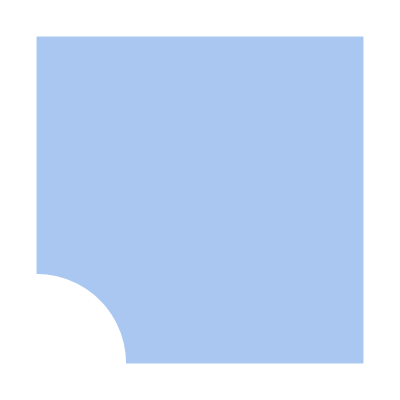

```mathematica
Region[region]
```

```mathematica
solc = NDSolveValue[
{lpc==NeumannValue[0,r==0&&a<z<b] + NeumannValue[0,z==0&&a<r<b],
DirichletCondition[ϕ[r,z]==-1,r^2+z^2==a^2],
ϕ[r,h/2]==0, ϕ[b,z]==0},ϕ, {r,z}∈region
]
```

InterpolatingFunction[…]

```mathematica
mesh = ToElementMesh[region,MaxCellMeasure->0.01]
```

ElementMesh[{{0.,7.3},{0.,7.3}},{TriangleElement[<7915>]}]

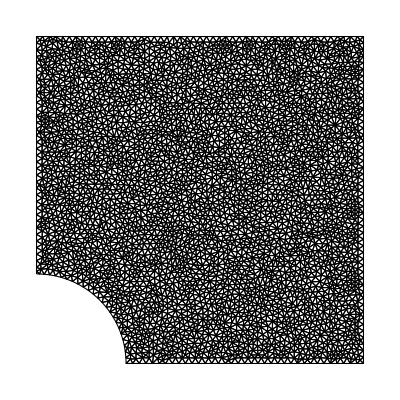

```mathematica
mesh["Wireframe"]
```

```mathematica
solc = NDSolveValue[
{lpc==NeumannValue[0,r==0&&a<z<b] + NeumannValue[0,z==0&&a<r<b],
DirichletCondition[ϕ[r,z]==-1,r^2+z^2==a^2],
ϕ[r,h/2]==0, ϕ[b,z]==0},ϕ, {r,z}∈mesh
]
```

InterpolatingFunction[…]

```mathematica
preciseSols=Table[Module[{val},
val=SetPrecision[solc[Abs[r],Abs[z]],5];
If[val===Indeterminate &&Sqrt[r^2+z^2]<=2,val=-1];
If[val===Indeterminate &&Sqrt[r^2+z^2]>=6,val=0];
SetPrecision[val,5]
],{z,0,7,0.01},{r,0,7,0.01}];
```

```mathematica
Dimensions[preciseSols]
```

{701,701}

```mathematica
preciseSols=Insert[preciseSols,"1/27/2023, William Bowers, a sphere-in-cylinder potential with a=2, b=7.3, h=14.6, 5 decimal places of precision, higher density mesh", 1];
preciseSols=Insert[preciseSols,"type cylindrical", 2];
preciseSols=Insert[preciseSols,{701, 701, 0.0001}, 3];
```

```mathematica
Export["/Users/wbowers/Downloads/fixed-sc-phi.txt",SetPrecision[preciseSols,5],"Table"]
```

/Users/wbowers/Downloads/fixed-sc-phi.txt

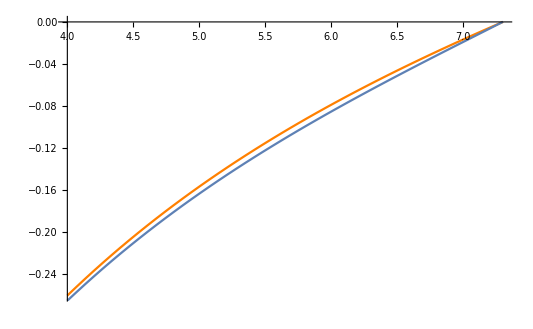

```mathematica
Show[Plot[solc[x,2],{x,4,7.3},PlotStyle->Orange],Plot[-GetPotential[1,x,0,2],{x,4,7.3}]]
```

```mathematica
GetPotential[1,7.3,0,2]
solc[7.3,2]
```

0.

-5.54157×10^-15

```mathematica
Table[100(-GetPotential[1,x,0,2]-solc[x,2])/solc[x,2],{x,2,7,0.1}]
```

{-0.000593962,0.0302143,0.0669475,0.107599,0.153567,0.205989,0.265234,0.330506,0.402651,0.479693,0.562935,0.65527,0.756071,0.862907,0.981737,1.1045,1.23865,1.38178,1.53412,1.70069,1.87417,2.05957,2.25555,2.46296,2.68104,2.91327,3.15904,3.4165,3.68993,3.97506,4.27771,4.59229,4.92959,5.27828,5.64014,6.02447,6.41774,6.83889,7.27547,7.7312,8.20665,8.70093,9.21675,9.7532,10.3124,10.8946,11.4977,12.1262,12.7771,13.4559,14.1573}

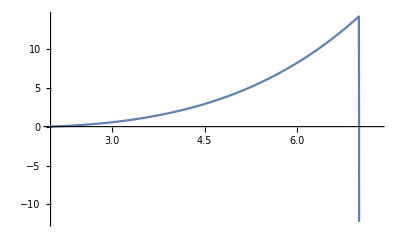

```mathematica
Plot[100(-GetPotential[1,x,0,2]-solc[x,2])/solc[x,2],{x,2,7.3}]
```

```mathematica
Plot[100(-GetPotential[1,0,0,z]-solc[z,2])/solc[z,2],{z,2,7.3}]
```

```mathematica
points=Reap[AvgElectronsEulerSC[53/100,1,15,2/5,99/100,True,10]][[2]]
```

1000 * RMS travel error: 1.77026

V/NC 1.5

λ: 53/100

Geometry: SC

Collisions: 10.01.3

Mean path: 8.8186

```mathematica
Show[Graphics3D[ {Opacity[0.3],Cylinder[{{0,0,-7.3},{0,0,7.3}},7.3]}],Graphics3D[Ball[{0,0,0},2]],Graphics3D[{Black,PointSize[0.01],Point[points[[1]]]}]]
```

-Graphics3D-

```mathematica
AvgElectronsEulerSC[53/100,10,15,1/5,4/5,True,500]
```

1000 * RMS travel error: 16.9994

V/NC 15.

λ: 53/100

Geometry: SC

Collisions: 157.8.

Mean path: 125.23

35.61.6

```mathematica
AvgElectronsEulerSC[λ_,Ni_,Ui_,dt_,tbound_,print_,count_] := Module[{eErrorList,V,E,result,stack,collisions,paths,svals,countbin,electronsbin,squaredbin,lbin,lbinSquared,data, seedcount,totalpaths,Nc},
V=Ui*Ni;
totalpaths=0;
paths={};
svals=0;
E=V/D;
seedcount=1;
collisions={};
eErrorList={};
countbin = Table[0,2/binwidth];
electronsbin =  Table[0,2/binwidth];
squaredbin= Table[0,2/binwidth];
lbin = Table[0,lmax/2+1];
lbinSquared =  Table[0,lmax/2+1,lmax/2+1];
data = {};
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,x1,y0,y1,z0,z1,numElectrons,cosθ,ϕ,s,vx,vy,vz, energy,eError,numCollisions,pathval,sval,idx,cθ0,ϕ0,SH,l,l2,collisionE,cost,phi,start,path,input},
numElectrons = 1; 
numCollisions=0;
stack["Push",GetStartingPos[]];
{cθ0,ϕ0} = GetAngles[x0,y0,z0];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
cosθ=1;
ϕ=0;
energy=0;
path=0;
While[
s=RandomVariate[ExponentialDistribution[1/λ],WorkingPrecision->16];

(*
Sow[Flatten[{"beginningPos/Vos",ToString[SetPrecision[#,7]]&/@{x0,y0,z0,vx,vy,vz}}]];
Sow[{"s",ToString[SetPrecision[s,15]]}];
*)

{x1,y1,z1, vx, vy, vz, energy,eError,pathval,sval}=GetNewPositionsEuler[dt,s,V,x0,y0,z0,vx,vy,vz];
If[x1!=100,Sow[{x1,y1,z1}]];
AppendTo[eErrorList,eError];

(*
Sow[Flatten[{"endingPos/Vos",ToString[SetPrecision[#,7]]&/@{x1,y1,z1,vx,vy,vz}}]];
*)

InBounds[x1,y1,z1],
path+=pathval;
AppendTo[paths,pathval];
svals+=s;
numCollisions++;
If[energy>=Ui,
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}];
energy-=Ui,
collisionE=SetPrecision[Ui*RandomVariate[UniformDistribution[{1/10, 1/2}]],16];

(*
Sow[{"collision energy",ToString[SetPrecision[collisionE,15]]}];
*)

energy-=collisionE;
If[energy<0,energy=0];
];
{vx, vy, vz, cost, phi}=UpdateVelocity[energy, vx, vy, vz, tbound];

(*
If[cost==100,Sow[{"cosTheta", "N/A"}],Sow[{"cosTheta", ToString[SetPrecision[cost,15]]}]];
If[phi==100,Sow[{"phi", "N/A"}],Sow[{"phi", ToString[SetPrecision[phi,15]]}]];
*)

{x0,y0,z0}={x1,y1,z1};
];
totalpaths+=path;
]; 
idx=FindBinNum[cθ0,binwidth];
countbin[[idx]]+=1;
electronsbin[[idx]]+=numElectrons;
squaredbin[[idx]]+=numElectrons^2;
SH=numElectrons Table[Conjugate[SphericalHarmonicY[l,0,ArcCos[cθ0],ϕ0]],{l,0,lmax,2}];
AppendTo[data,{ArcCos[cθ0],ϕ0,numElectrons}];
For[l= 0, l <= lmax, l+=2,
lbin[[l/2+1]]+=SH[[l/2+1]];
For[l2=0,l2<=lmax,l2+=2,
lbinSquared[[l/2+1,l2/2+1]]+=SH[[l/2+1]]SH[[l2/2+1]]
]
];
AppendTo[collisions,numCollisions];
numElectrons],
{count}];
If[print,
Print["1000 * RMS travel error: ",1000*RootMeanSquare[eErrorList]];
Print["V/NC ",Ni Ui λ/5.3];
Print["λ: ",λ];
Print["Geometry: ",ID];
Print["Collisions: ", Around[Mean[collisions],StandardDeviation[collisions]/Sqrt[count]]];
Print["Mean path: ",  totalpaths/count/λ];
];
(*Sow[{countbin,electronsbin, squaredbin,lbin,lbinSquared,data}];*)
Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

```mathematica
MaxElectrons[1/2,7,1000]
```

{11.590.10,11.300.10,11.230.11,11.140.10,11.750.09,12.330.10,10.160.07,12.190.08,11.880.09,12.800.11}

12.00.6

```mathematica
MaxElectrons[1,5,200]
```

{5.830.09,5.860.07,6.170.14,6.110.11,5.670.20,5.380.11,5,6.500.12,7.000.10,6.800.05}

6.20.8

```mathematica
ListPlot[{5.830.09,5.860.07,6.170.14,6.110.11,5.670.20,5.380.11,5,6.500.12,7.000.10,6.800.05}]
```

```mathematica
maxes=Table[{Ni,MaxElectrons[1/2,Ni,250]},{Ni,3,11,2}]
```

{1.4290.031,2.000.04,1.800.04,1.830.06,2,1.500.05,1.5000.032,2,1.890.04,2.5000.032}

{5.380.09,4.600.05,5.000.07,4.000.04,5.400.09,4.330.09,4.570.06,5.000.06,5.140.07,5.000.09}

{11.220.20,11.600.20,13.290.22,11.800.19,9.860.12,14.330.20,12.000.06,11.130.22,13.000.24,11.400.14}

{27.40.6,21.80.4,21.600.10,20.00.4,27.50.6,25.50.4,19.30.6,22.40.7,20.00.4,21.30.7}

{39.51.3,47.31.7,53.31.0,63.01.3,40.91.1,50.71.2,49.30.8,27.71.0,50.61.3,43}

{{3,2.000.08},{5,5.80.5},{7,12.41.6},{9,30.4.},{11,53.93.4}}

```mathematica
listForFit = {#[[1]],#[[2,1]]}&/@maxes;
errorslist = #[[2,2]]&/@maxes;
Clear[p1, p2, p3];
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
Print[fit["BestFitParameters"]];
f=(Log[(25-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
res=Around[f,Sqrt[error]]/.fit["BestFitParameters"]
```

{p1→1.52354,p2→0.328429,p3→-2.08025}

8.760.09

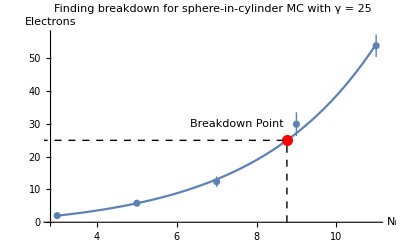

```mathematica
Show[ListPlot[maxes],Plot[fit[x],{x,3,11}],Graphics[{Red,PointSize[0.02],Point[{res[[1]],25}]}],Graphics[{Dashed,Black,Line[{{0,25},{res[[1]],25}}],Line[{{res[[1]],0},{res[[1]],25}}]}],Graphics[Text[Breakdown Point,{7.5,30}]],AxesLabel->{Subscript[N,i],Electrons},PlotLabel->"Finding breakdown for sphere-in-cylinder MC with γ = 25"]
```

```mathematica
MaxElectrons[53/100,10,1500]
```

$Aborted

```mathematica
MaxElectrons[λ_,Ni_,reps_]:= Module[{idx,errors,electronsPart,list, bins,i,thetaslist,constants,SHYs,fit,max,error},
bins =Last[Last[Last[Reap[AvgElectronsEulerSC[λ,Ni,15,2/5,4/5,True,reps] ]]]];
errors =Sqrt[bins[[3]]/bins[[1]] -(bins[[2]]/bins[[1]])^2]/Sqrt[reps];
electronsPart=Table[Around[(bins[[2]]/bins[[1]])[[i]],errors[[i]]],{i,1,10}];
list = bins[[6]];
Print[electronsPart];
fit=LinearModelFit[list,Table[SphericalHarmonicY[l,0,θ,ϕ],{l,0,lmax,2}],{θ,ϕ},IncludeConstantBasis->False];
Clear[t];
max=NMaximize[fit[t,0],{t,0,Pi}];
SHYs=Table[SphericalHarmonicY[l,0,t,0],{l,0,lmax,2}];
error = Sqrt[SHYs.fit["CovarianceMatrix"].Transpose[SHYs]]/.max[[2]];
Around[max[[1]],error]
]
```

```mathematica
r=Reap[AvgElectronsEulerSC[2,10,15,2/5,4/5,True,100000]];
```

1000 * RMS travel error: 35.7023

λ: 2

Geometry: SC

Collisions: 8.7130.024

Mean path: 4.53573

6.890.04

{{-0.975,6.6900.015},{-0.925,6.6530.015},{-0.875,6.6860.015},{-0.825,6.4250.014},{-0.775,6.6840.015},{-0.725,6.2100.014},{-0.675,6.3400.014},{-0.625,6.6760.015},{-0.575,6.5380.015},{-0.525,6.4900.015},{-0.475,6.5060.015},{-0.425,6.5310.014},{-0.375,6.5620.015},{-0.325,6.9140.016},{-0.275,6.6770.015},{-0.225,6.6050.015},{-0.175,6.8160.016},{-0.125,6.9970.016},{-0.075,6.9550.015},{-0.025,6.8010.015},{0.025,6.9460.016},{0.075,6.6700.015},{0.125,6.9190.016},{0.175,6.8940.016},{0.225,6.9880.016},{0.275,6.5910.015},{0.325,6.6520.015},{0.375,6.5870.015},{0.425,6.6850.015},{0.475,6.5450.015},{0.525,6.2770.014},{0.575,6.4720.014},{0.625,6.8310.015},{0.675,6.4900.015},{0.725,6.3890.014},{0.775,6.6420.015},{0.825,6.6250.015},{0.875,6.7420.015},{0.925,6.7300.015},{0.975,6.8200.016}}

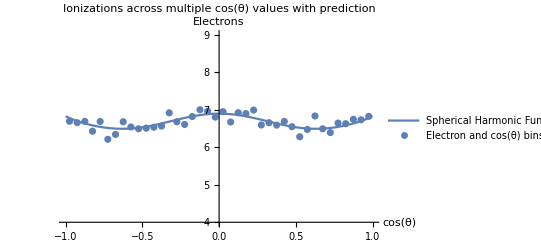

```mathematica
bins=r[[2,1,1]];
errors =Sqrt[bins[[3]]/bins[[1]] -(bins[[2]]/bins[[1]])^2]/Sqrt[100000];
electronsPart=Table[Around[(bins[[2]]/bins[[1]])[[i]],errors[[i]]],{i,1,40}];
list = bins[[6]];
fit=LinearModelFit[list,Table[SphericalHarmonicY[l,0,θ,ϕ],{l,0,8,2}],{θ,ϕ},IncludeConstantBasis->False];
Clear[t];
max=NMaximize[fit[t,0],{t,0,Pi}];
SHYs=Table[SphericalHarmonicY[l,0,t,0],{l,0,8,2}];
error = Sqrt[SHYs.fit["CovarianceMatrix"].Transpose[SHYs]]/.max[[2]];
Around[max[[1]],error]
electrons=Transpose[{Table[theta,{theta,-0.975,0.975,0.05}],electronsPart}]
Show[Plot[fit[ArcCos[theta],0],{theta,-1,1},PlotRange->{4,9},PlotLegends->{"Spherical Harmonic Function"}],ListPlot[electrons,PlotLegends->{"Electron and cos(θ) bins "}],AxesLabel->{"cos(θ)",Electrons},PlotLabel->"Ionizations across multiple cos(θ) values with prediction"]
```

```mathematica
|
```

Change l value and look at r^2

{{0.2,1},{1.,1.3180.015},{1.8,1.8450.026},{2.6,2.830.05},{3.4,3.990.08},{4.2,5.920.13},{5.,8.460.25},{5.8,12.90.4},{6.6,19.10.6},{7.4,27.81.1}}

{{0.2,1},{1.,1.290.05},{1.8,2.300.11},{2.6,3.450.19},{3.4,6.140.35},{4.2,10.10.6},{5.,17.30.9},{5.8,29.51.6},{6.6,44.42.6},{7.4,85.5.}}

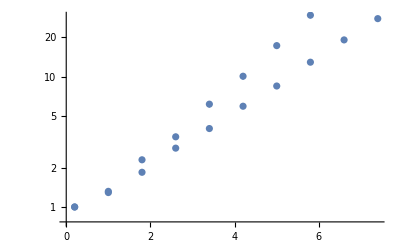

```mathematica
test1=Table[{Nc,AvgElectronsWeighted[Nc,2Nc,1000] },{Nc,0.2,8,0.8}]
test2=Table[{Nc,AvgElectrons3D[Nc,2Nc,5,1,0.8,100]},{Nc,0.2,8,0.8}]
Show[ListLogPlot[test1],ListLogPlot[test2]]
```

```mathematica
t1=Table[{Nc,AvgElectronsWeighted[Nc,Nc,1000] },{Nc,0.2,14,0.8}]
```

{{0.2,1},{1.,1},{1.8,1.2560.014},{2.6,1.6120.018},{3.4,2.0060.029},{4.2,2.550.04},{5.,3.170.06},{5.8,3.890.07},{6.6,4.890.10},{7.4,6.000.13},{8.2,7.960.17},{9.,9.470.22},{9.8,12.350.32},{10.6,14.90.4},{11.4,19.70.5},{12.2,23.30.6},{13.,28.90.9},{13.8,36.81.1}}

```mathematica
t1={{0.2,1},{1.,1},{1.8,1.2560.014},{2.6000000000000005,1.6120.018},{3.4000000000000004,2.0060.029},{4.2,2.550.04},{5.000000000000001,3.170.06},{5.800000000000001,3.890.07},{6.6000000000000005,4.890.10},{7.4,6.000.13},{8.2,7.960.17},{9.,9.470.22},{9.8,12.350.32},{10.6,14.90.4},{11.4,19.70.5},{12.2,23.30.6},{13.,28.90.9},{13.8,36.81.1}}
```

{{0.2,1},{1.,1},{1.8,1.2560.014},{2.6,1.6120.018},{3.4,2.0060.029},{4.2,2.550.04},{5.,3.170.06},{5.8,3.890.07},{6.6,4.890.10},{7.4,6.000.13},{8.2,7.960.17},{9.,9.470.22},{9.8,12.350.32},{10.6,14.90.4},{11.4,19.70.5},{12.2,23.30.6},{13.,28.90.9},{13.8,36.81.1}}

```mathematica
java1d={{0.2,Around[1.0,0.0]},{1.0,Around[1.0,0.0]},{1.8,Around[1.292,0.0]},{2.6,Around[1.6152,0.0]},{3.4000000000000004,Around[2.0128,0.0]},{4.2,Around[2.5308,0.0]},{5.0,Around[3.1744,0.0]},{5.8,Around[3.96,0.0]},{6.6,Around[4.8992,0.0]},{7.3999999999999995,Around[6.146,0.0]},{8.2,Around[7.778,0.0]},{9.0,Around[9.6872,0.0]},{9.8,Around[11.818,0.0]},{10.600000000000001,Around[14.9372,0.0]},{11.400000000000002,Around[18.5404,0.0]},{12.200000000000003,Around[22.9588,0.0]},{13.000000000000004,Around[29.3304,0.0]},{13.800000000000004,Around[36.6168,0.0]},{14.600000000000005,Around[45.6408,0.0]}}
```

{{0.2,1.},{1.,1.},{1.8,1.292},{2.6,1.6152},{3.4,2.0128},{4.2,2.5308},{5.,3.1744},{5.8,3.96},{6.6,4.8992},{7.4,6.146},{8.2,7.778},{9.,9.6872},{9.8,11.818},{10.6,14.9372},{11.4,18.5404},{12.2,22.9588},{13.,29.3304},{13.8,36.6168},{14.6,45.6408}}

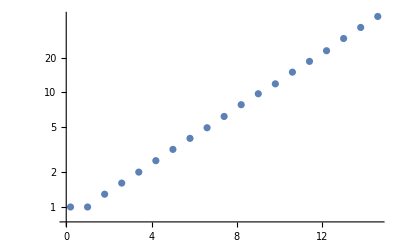

```mathematica
ListLogPlot[java1d]
```

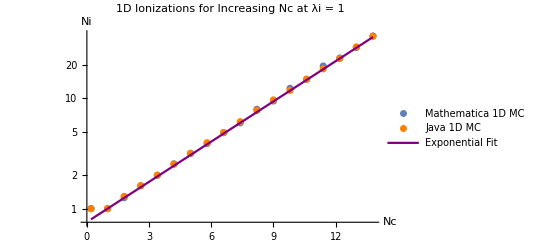

```mathematica
Show[ListLogPlot[t1,PlotLegends->{"Mathematica 1D MC"}],ListLogPlot[java1d,PlotStyle->Orange,PlotLegends->{"Java 1D MC"}],LogPlot[Exp[0.28(x-1)],{x,0.2,13.8},PlotStyle->Purple,PlotLegends->{"Exponential Fit"}],PlotLabel->"1D Ionizations for Increasing Nc at λi = 1",AxesLabel->{Nc,Ni}]
```

```mathematica
t2=Table[{Nc,AvgElectrons3D[Nc,Nc,5,15,0.8,100]},{Nc,0.2,14,0.8}]
```

{{0.2,1},{1.,1},{1.8,1.360.05},{2.6,1.880.07},{3.4,2.540.10},{4.2,3.410.14},{5.,5.310.20},{5.8,6.940.29},{6.6,10.150.35},{7.4,13.90.5},{8.2,20.60.7},{9.,26.21.0},{9.8,36.71.1},{10.6,51.31.7},{11.4,74.42.6},{12.2,102.13.3},{13.,136.5.},{13.8,195.7.}}

```mathematica
java3d={{0.2,Around[1.0,0.0]},{1.0,Around[1.0,0.0]},{1.8,Around[1.3708,0.009660380116744999]},{2.6,Around[1.8896,0.014252183552003757]},{3.4000000000000004,Around[2.6092,0.01951076994892846]},{4.2,Around[3.622,0.02711690247797481]},{5.0,Around[5.0172,0.03788458346082171]},{5.8,Around[7.038,0.05230891319842165]},{6.6,Around[9.6412,0.071414459488258]},{7.3999999999999995,Around[13.5272,0.0970370241918007]},{8.2,Around[18.8308,0.13820415530656086]},{9.0,Around[26.5088,0.18488258172148112]},{9.8,Around[36.892,0.25806691845333396]},{10.600000000000001,Around[51.484,0.353070726059242]},{11.400000000000002,Around[71.3404,0.49144933730344953]},{12.200000000000003,Around[98.8472,0.6953129517447517]},{13.000000000000004,Around[139.1028,0.961511358676537]},{13.800000000000004,Around[194.0804,1.3399496611201482]}}
```

{{0.2,1.},{1.,1.},{1.8,1.3710.010},{2.6,1.8900.014},{3.4,2.6090.020},{4.2,3.6220.027},{5.,5.020.04},{5.8,7.040.05},{6.6,9.640.07},{7.4,13.530.10},{8.2,18.830.14},{9.,26.510.18},{9.8,36.890.26},{10.6,51.480.35},{11.4,71.30.5},{12.2,98.80.7},{13.,139.11.0},{13.8,194.11.3}}

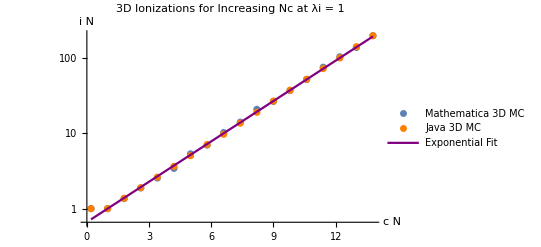

```mathematica
Show[ListLogPlot[t2,PlotLegends->{"Mathematica 3D MC"}],ListLogPlot[java3d,PlotStyle->Orange,PlotLegends->{"Java 3D MC"}],LogPlot[Exp[0.41(x-1)],{x,0.2,13.8},PlotStyle->Purple,PlotLegends->{"Exponential Fit"}],PlotLabel->"3D Ionizations for Increasing Nc at λi = 1",AxesLabel->{Nc,Ni}]
```

## Exploring 1D alpha

```mathematica
FindAlpha[λi_] := Module[{electrons,result,length,i,total,slopes,alpha,e},
electrons = Table[{Nc,AvgElectronsWeighted[Nc,((1/λi) Nc),500]},{Nc,λi+1,20,0.5}];
alpha = Mean[Table[Log[e[[2]] ]/(e[[1]] -λi),{e,electrons}]];
alpha]
```

```mathematica
FindAlpha[1]
```

0.28450.0009

```mathematica
javaalphas={{0.25,Around[0.6602595438326849,0.001904193660625115]},{0.5,Around[0.47844948673235005,0.001748144153630099]},{0.75,Around[0.35821274297950323,0.0031233087246661244]},{1.0,Around[0.27433365451618424,0.008691189348246631]},{1.25,Around[0.21314895885656557,0.013389317555812227]},{1.5,Around[0.1669038047699682,0.01749867647681158]},{1.75,Around[0.13018046550569878,0.014267346022973922]},{2.0,Around[0.1015082557377325,0.012894206875325626]},{2.2500000000000004,Around[0.078742597634773,0.011952013460590393]},{2.5,Around[0.061520625296323746,0.010962062286845231]},{2.75,Around[0.04725434577446056,0.00734274289001424]},{3.0,Around[0.0358071249036958,0.004959892432166247]},{3.25,Around[0.02778741774482209,0.004504199943380026]},{3.5,Around[0.021572007247372436,0.003796229153906858]},{3.7500000000000004,Around[0.015726014436025514,0.0022654561964774527]},{4.0,Around[0.012178682642516597,0.0017503399885901638]},{4.25,Around[0.008830658060106817,0.0010123646555449694]}}
```

{{0.25,0.66030.0019},{0.5,0.47840.0017},{0.75,0.35820.0031},{1.,0.2740.009},{1.25,0.2130.013},{1.5,0.1670.017},{1.75,0.1300.014},{2.,0.1020.013},{2.25,0.0790.012},{2.5,0.0620.011},{2.75,0.0470.007},{3.,0.0360.005},{3.25,0.0280.005},{3.5,0.0220.004},{3.75,0.01570.0023},{4.,0.01220.0018},{4.25,0.00880.0010}}

```mathematica
alphas1d=Table[{r,FindAlpha[r]},{r,0.25,4.25,0.25}]
```

{{0.25,0.66000.0024},{0.5,0.48420.0013},{0.75,0.36740.0010},{1.,0.28430.0009},{1.25,0.22570.0009},{1.5,0.17670.0008},{1.75,0.14090.0008},{2.,0.11280.0008},{2.25,0.08970.0007},{2.5,0.07170.0007},{2.75,0.05730.0007},{3.,0.04590.0006},{3.25,0.03520.0006},{3.5,0.02760.0005},{3.75,0.02160.0005},{4.,0.01740.0004},{4.25,0.01370.0004}}

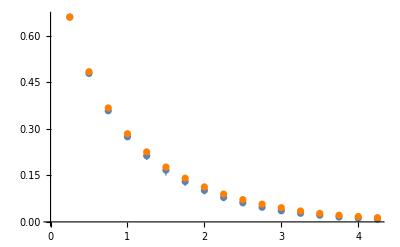

```mathematica
Show[ListPlot[javaalphas],ListPlot[alphas1d,PlotStyle->Orange]]
```

```mathematica
alphaVals = Table[{λi,FindAlpha[λi]},{λi,1/4,4,1/2}]
alphav2Vals = Table[{λi,Exp[-λi]},{λi,1/4,4,1/2}] //N
```

{{1/4,0.66290.0027},{3/4,0.36500.0010},{5/4,0.22440.0009},{7/4,0.14110.0008},{9/4,0.09120.0008},{11/4,0.05770.0007},{13/4,0.03630.0006},{15/4,0.02210.0005}}

{{0.25,0.778801},{0.75,0.472367},{1.25,0.286505},{1.75,0.173774},{2.25,0.105399},{2.75,0.0639279},{3.25,0.0387742},{3.75,0.0235177}}

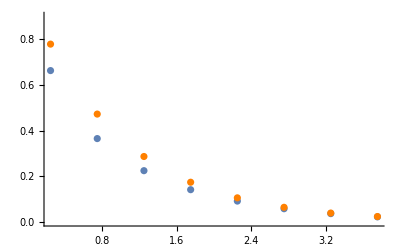

```mathematica
Show[ListPlot[alphaVals],ListPlot[alphav2Vals,PlotStyle->Orange],PlotRange->{0,0.9}]
```

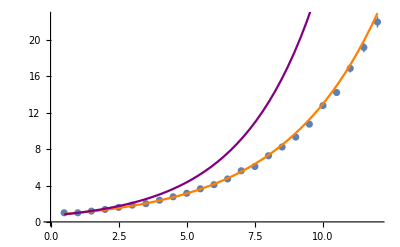

```mathematica
λi=1;
testVals = Table[{Nc,AvgElectronsWeighted[Nc,(1/λi) Nc,1000]},{Nc,1/2,12,1/2}];
α = FindAlpha[λi][[1]];
α2 = Exp[-λi];
Show[ListPlot[testVals],Plot[Exp[α (Nc-λi)],{Nc,1/2,12},PlotStyle->Orange],Plot[Exp[α2( Nc-λi)],{Nc,1/2,12},PlotStyle->Purple]]
```

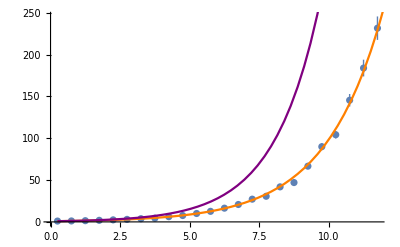

```mathematica
λi=1/2;
testVals = Table[{Nc,AvgElectronsWeighted[Nc,(1/λi) Nc,1000]},{Nc,1/4,12,1/2}];
α = FindAlpha[λi][[1]];
α2 = Exp[-λi];
Show[ListPlot[testVals],Plot[Exp[α (Nc-λi)],{Nc,1/4,12},PlotStyle->Orange],Plot[Exp[α2( Nc-λi)],{Nc,1/4,12},PlotStyle->Purple]]
```

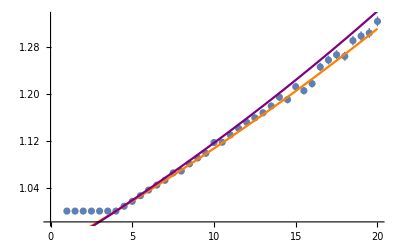

```mathematica
λi=4;
testVals = Table[{Nc,AvgElectronsWeighted[Nc,(1/λi) Nc,5000]},{Nc,1,20,1/2}];
α = FindAlpha[λi][[1]];
α2 = Exp[-λi];
Show[ListPlot[testVals],Plot[Exp[α (Nc-λi)],{Nc,1,20},PlotStyle->Orange],Plot[Exp[α2( Nc-λi)],{Nc,1,20},PlotStyle->Purple]]
```

## Alpha equation with x (reference alpha derivation)

```mathematica
l1 = Reap[AvgElectrons3D[10,10,5000]]; l1[[1]]
```

39.790.19

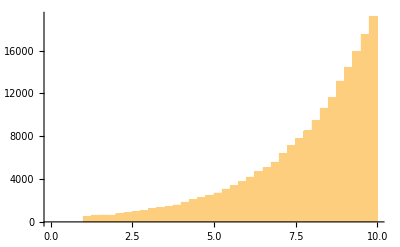

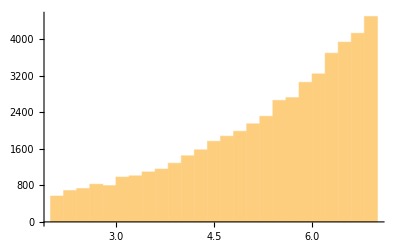

```mathematica
Histogram[l1[[2,1]],{0,10,0.25}]
Histogram[l1[[2,1]],{2,7,0.2}]
```

```mathematica
Clear[α]
FindAlphav2[λi_,x_]:= (Exp[-λi] - Exp[-x])/(1-Exp[-x])
Plot3D[FindAlphav2[λi,x],{λi,1/2,4},{x,1/2,5},AxesLabel->{λi,x,α}]
```

-Graphics3D-

```mathematica
FindRoot[FindAlphav2[1/2,x]==FindAlpha[1/2][[1]],{x,1,6}]
FindRoot[FindAlphav2[1,x]==FindAlpha[1][[1]],{x,1,6}]
FindRoot[FindAlphav2[4,x]==FindAlpha[4][[1]],{x,1,6}]
```

{x→1.42628}

{x→2.16402}

{x→6.78437}

12.650.06

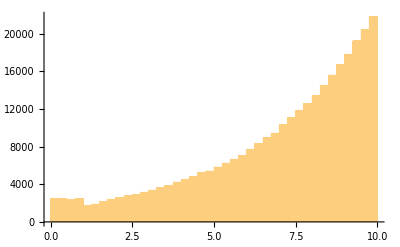

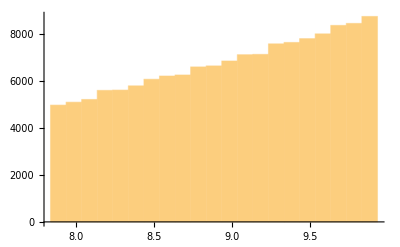

```mathematica
l1 = Reap[AvgElectronsBanked[10,10,10000]]; l1[[1]]
Histogram[l1[[2,1]],{0,10,0.25}]
Histogram[l1[[2,1]],{(10-2.16401),10,0.1}]
```

7.250.04

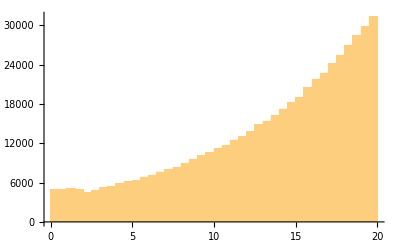

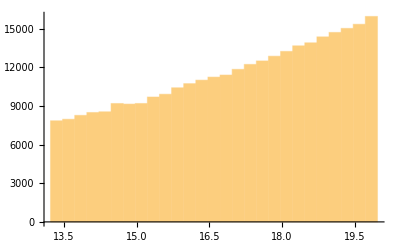

```mathematica
l2= Reap[AvgElectronsBanked[20,10,10000]]; l2[[1]]
Histogram[l2[[2,1]],{0,20,0.5}]
Histogram[l2[[2,1]],{20-6.78,20,0.25}]
```

95.40.5

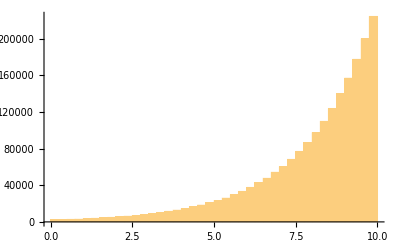

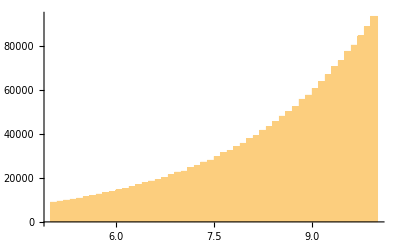

```mathematica
l3 = Reap[AvgElectronsBanked[10,20,10000]]; l3[[1]]
Histogram[l3[[2,1]],{0,10,0.25}]
Histogram[l3[[2,1]],{10-5,10,0.1}]
```

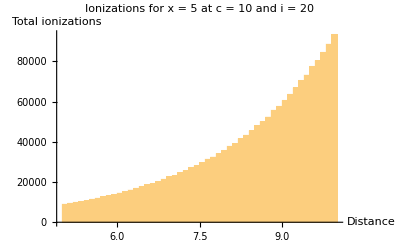

```mathematica
Histogram[l3[[2,1]],{10-5,10,0.1},AxesLabel->{"Distance", "Total ionizations"},PlotLabel->"Ionizations for x = 5 at c = 10 and i = 20"]
```

```mathematica
FindKink[λi_] := Module[{idx,electrons,positions,result,length,i,total,slopes,alpha,e},
electrons = Table[{d,AvgElectrons3D[d,(1/λi) d,d,15,50]},{d,λi/50, λi+0.3, 0.025}];
positions=Position[electrons,1];
idx=First[Last[positions]];
electrons[[idx,1]]];
```

```mathematica
FindKink[1/5]
```

{{0.004,1},{0.029,1},{0.054,1},{0.079,1},{0.104,1},{0.129,1},{0.154,1},{0.179,1},{0.204,1},{0.229,1},{0.254,1.0200.020},{0.279,1.0600.034},{0.304,1.0600.034},{0.329,1.080.04},{0.354,1.080.04},{0.379,1.0400.028},{0.404,1.200.06},{0.429,1.220.06},{0.454,1.180.05},{0.479,1.240.07}}

0.229

```mathematica
Table[{x,FindKink[x]},{x,0.25,5.75,0.5}]
```

{{0.25,0.25},{0.75,0.75},{1.25,1.25},{1.75,1.75},{2.25,2.65},{2.75,2.95},{3.25,3.45},{3.75,4.05},{4.25,4.75},{4.75,5.25},{5.25,5.75},{5.75,6.25}}

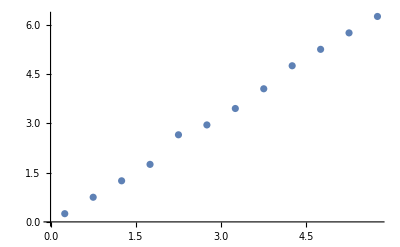

```mathematica
ListPlot[%]
```

## Plotting breakdown

```mathematica
FindBreakdown[r_,γ_] := Module[{alpha, idx,Nc, Ni},
alpha = FindAlpha[r];
Nc = Log[γ]/alpha + r ;
Ni = (1/r)(Nc);
{Nc,Ni}]
```

```mathematica
FindBreakdown[1,50]
```

{14.770.04,14.770.04}

```mathematica
FindBreakdown[5,50]
```

{588.26.,118.5.}

```mathematica
bdVals = Table[FindBreakdown[r,50],{r,1/50,5,1/4}]
```

{{4.1640.024,208.21.2},{6.3750.020,23.610.08},{8.8350.023,16.990.04},{11.7000.031,15.190.04},{15.050.05,14.760.04},{19.040.07,14.990.05},{24.090.11,15.850.07},{29.820.16,16.850.09},{37.480.25,18.550.12},{47.10.4,20.750.17},{59.10.6,23.450.22},{71.00.8,25.650.29},{92.21.2,30.50.4},{119.11.9,36.40.6},{145.12.7,41.20.8},{189.4.,50.11.1},{234.6.,58.31.5},{292.8.,68.31.9},{369.13.,81.62.8},{476.19.,100.4.}}

```mathematica
bd1d ={{4.164±0.024,208.2±1.2},{6.375±0.020,23.61±0.08},{8.835±0.023,16.99±0.04},{11.700±0.031,15.19±0.04},{15.05±0.05,14.76±0.04},{19.04±0.07,14.99±0.05},{24.09±0.11,15.85±0.07},{29.82±0.16,16.85±0.09},{37.48±0.25,18.55±0.12},{47.1±0.4,20.75±0.17},{59.1±0.6,23.45±0.22},{71.0±0.8,25.65±0.29},{92.2±1.2,30.5±0.4},{119.1±1.9,36.4±0.6},{145.1±2.7,41.2±0.8},{189.±4.,50.1±1.1},{234.±6.,58.3±1.5},{292.±8.,68.3±1.9},{369.±13.,81.6±2.8},{476.±19.,100.±4.},{588.±26.,118.±5.}}
```

{{4.164±0.024,208.2±1.2},{6.375±0.02,23.61±0.08},{8.835±0.023,16.99±0.04},{11.7±0.031,15.19±0.04},{15.05±0.05,14.76±0.04},{19.04±0.07,14.99±0.05},{24.09±0.11,15.85±0.07},{29.82±0.16,16.85±0.09},{37.48±0.25,18.55±0.12},{47.1±0.4,20.75±0.17},{59.1±0.6,23.45±0.22},{71.±0.8,25.65±0.29},{92.2±1.2,30.5±0.4},{119.1±1.9,36.4±0.6},{145.1±2.7,41.2±0.8},{189.±4.,50.1±1.1},{234.±6.,58.3±1.5},{292.±8.,68.3±1.9},{369.±13.,81.6±2.8},{476.±19.,100.±4.},{588.±26.,118.±5.}}

```mathematica
javabd={{Around[5.700231943597744,0.01207241166528697],Around[28.50115971798872,0.06036205832643485]},{Around[5.79873973252985,0.008127368263246374],Around[27.61304634538024,0.03870175363450654]},{Around[5.90510885004121,0.01880097208443146],Around[26.841403863823686,0.08545896402014301]},{Around[5.980782139922633,0.022623892171313394],Around[26.00340060835927,0.09836474857092779]},{Around[6.174977597021277,0.017808683425452585],Around[24.699910388085108,0.07123473370181034]},{Around[6.259659518165803,0.01294585426723786],Around[24.075613531406933,0.049791747181684075]},{Around[6.453798986162792,0.02814262266653645],Around[23.049282093438542,0.1005093666662016]},{Around[6.750213589096242,0.005356209559882019],Around[21.774882545471748,0.017278095354458126]},{Around[6.956648887715002,0.006510191038770662],Around[21.08075420519698,0.01972785163263837]},{Around[7.220958181081789,0.016024550705824953],Around[20.058217169671636,0.04451264084951376]},{Around[7.635908775222859,0.010276886691871264],Around[19.089771938057147,0.02569221672967816]},{Around[8.03464133984749,0.0036999717907642495],Around[18.260548499653385,0.008409026797191476]},{Around[8.666186577739973,0.01778912290701574],Around[17.332373155479946,0.03557824581403148]},{Around[9.350404990874567,0.006419931102432235],Around[16.69715176941887,0.011464162682914704]},{Around[10.558215754398047,0.018609784723081196],Around[15.997296597572799,0.028196643519819993]},{Around[12.189849737655585,0.1691424999247856],Around[15.430189541336182,0.2141044302845387]},{Around[15.233034583855726,0.5468246433362867],Around[15.233034583855726,0.5468246433362867]},{Around[32.607032745474434,3.5391212217852397],Around[18.422052398573125,1.9995035151329037]},{Around[37.56666730405342,4.788665312298926],Around[19.56597255419449,2.494096516822358]},{Around[51.5143029936392,7.969622234516992],Around[22.895245774950755,3.5420543264519964]},{Around[226.1883191276727,34.15818691413011],Around[61.13197814261424,9.231942409224354]},{Around[312.9949279966182,39.66595313492955],Around[78.24873199915454,9.916488283732388]}}
```

{{5.7000.012,28.500.06},{5.7990.008,27.610.04},{5.9050.019,26.840.09},{5.9810.023,26.000.10},{6.1750.018,24.700.07},{6.2600.013,24.080.05},{6.4540.028,23.050.10},{6.7500.005,21.7750.017},{6.9570.007,21.0810.020},{7.2210.016,20.060.04},{7.6360.010,19.0900.026},{8.0350.004,18.2610.008},{8.6660.018,17.330.04},{9.3500.006,16.6970.011},{10.5580.019,15.9970.028},{12.190.17,15.430.21},{15.20.5,15.20.5},{32.63.5,18.42.0},{38.5.,19.62.5},{52.8.,22.93.5},{226.34.,61.9.},{313.40.,78.10.}}

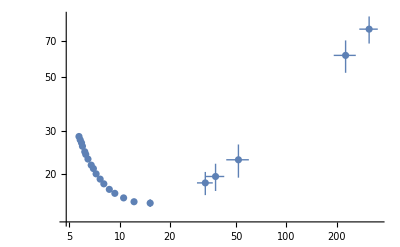

```mathematica
ListLogLogPlot[javabd]
```

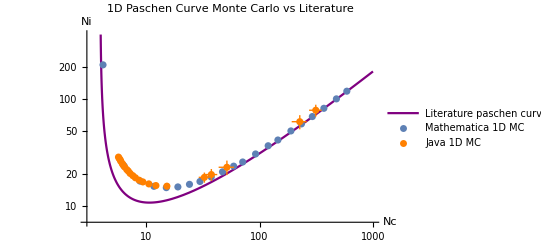

```mathematica
Show[LogLogPlot[Nc/(Log[Nc]-Log[Log[51]]),{Nc,3.9,1000},PlotRange->{{3,1000},{7,400}},PlotStyle->Purple,PlotLegends->{"Literature paschen curve"}],ListLogLogPlot[bd1d,PlotLegends->{"Mathematica 1D MC"}],ListLogLogPlot[javabd,PlotStyle->Orange,PlotLegends->{"Java 1D MC"}],AxesLabel->{"Nc","Ni"},PlotLabel->"1D Paschen Curve Monte Carlo vs Literature"]
```

```mathematica
FindBreakdown3D[d_,γ_,tbound_,Ni0_,reps_]:=Module[{region,list,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
list = Table[{Ni,AvgElectrons3D[d,Ni,d,15,tbound,reps] },{Ni,Ni0-3,Ni0+3}];
listForFit = {#[[1]],#[[2,1]]}&/@list;
errorslist = #[[2,2]]&/@list;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
FindBreakdown3Dv2[4.5,50,0.8,30,3000]
```

{{27,45.50.7},{28,46.10.7},{29,47.50.7},{30,48.50.7},{31,48.70.8},{32,49.90.8},{33,51.30.8}}

32.010.21

```mathematica
left=Table[{d,FindBreakdown3Dv2[d,50,0.8,20,500]},{d,5,6,0.5}]
```

{{5.,21.20.4},{5.5,16.750.35},{6.,11.5.}}

```mathematica
min=Table[{d,FindBreakdown3Dv2[d,50,0.8,10,100]},{d,6,16.5,2}]
```

{{6,14.40.4},{8,11.730.13},{10,10.7900.034},{12,10.600.04},{14,10.520.07},{16,10.700.05}}

```mathematica
right2=Table[{d,FindBreakdown3Dv2[d,50,0.8,13,50]},{d,17,57,4}]
```

{{17,10.810.08},{21,11.240.04},{25,12.070.09},{29,12.660.05},{33,13.450.05},{37,14.2550.029},{41,14.9390.018},{45,15.660.09},{49,16.490.22},{53,17.480.09},{57,17.740.30}}

```mathematica
right3=Table[{d,FindBreakdown3Dv2[d,50,0.8,17,25]},{d,60,100,8}]
```

{{60,18.520.09},{68,19.970.07},{76,21.310.35},{84,23.71.2},{92,24.70.9},{100,26.21.4}}

```mathematica
bdfinal={{4.5,32.010.21},{5.,21.20.4},{5.5,16.750.35},{6,14.40.4},{8,11.730.13},{10,10.7900.034},{12,10.600.04},{14,10.520.07},{16,10.700.05},{17,10.770.06},{20,11.180.06},{23,11.640.07},{26,12.210.06},{32,13.270.05},{37,14.2550.029},{41,14.9390.018},{49,16.490.22},{60,18.520.09},{76,21.310.35},{92,24.70.9},{100,26.21.4}}
```

{{4.5,32.010.21},{5.,21.20.4},{5.5,16.750.35},{6,14.40.4},{8,11.730.13},{10,10.7900.034},{12,10.600.04},{14,10.520.07},{16,10.700.05},{17,10.770.06},{20,11.180.06},{23,11.640.07},{26,12.210.06},{32,13.270.05},{37,14.2550.029},{41,14.9390.018},{49,16.490.22},{60,18.520.09},{76,21.310.35},{92,24.70.9},{100,26.21.4}}

```mathematica
bd3dold={{2.3250.033,69.71.0},{2.4340.034,48.70.7},{4.420.06,14.720.19},{6.680.10,12.150.18},{9.100.16,11.370.20},{11.710.24,11.150.23},{15.40.4,11.820.34},{18.20.6,11.70.4},{22.30.9,12.40.5},{26.81.3,13.10.6},{32.81.9,14.30.8},{36.72.2,14.40.9},{47.4.,16.71.3},{65.02.0,20.00.6},{78.72.9,22.50.8},{109.5.,29.01.3}}
```

{{2.3250.033,69.71.0},{2.4340.034,48.70.7},{4.420.06,14.720.19},{6.680.10,12.150.18},{9.100.16,11.370.20},{11.710.24,11.150.23},{15.40.4,11.820.34},{18.20.6,11.70.4},{22.30.9,12.40.5},{26.81.3,13.10.6},{32.81.9,14.30.8},{36.72.2,14.40.9},{47.4.,16.71.3},{65.02.0,20.00.6},{78.72.9,22.50.8},{109.5.,29.01.3}}

```mathematica
datav2={{Around[3.9349346617986107,0.004098654929587719],100},{7.,Around[12.5973499575545,0.021042290566655936]},{10.,Around[10.665900655226146,0.01147892717515875]},{20.,Around[11.199362729457336,0.0055071173430502485]},{40.,Around[14.831063909226039,0.011373607275817859]},{80.,Around[22.424620315119526,0.003938560064511855]},{160.,Around[36.60786133347448,0.009721595486457082]},{320.,Around[62.54053716519399,0.01924587067710669]},{640.,Around[109.85816366329091,0.022422691194965906]}}
```

{{3.9350.004,100},{7.,12.5970.021},{10.,10.6660.011},{20.,11.1990.006},{40.,14.8310.011},{80.,22.4250.004},{160.,36.6080.010},{320.,62.5410.019},{640.,109.8580.022}}

```mathematica
javabd={{5,21.273},{10,10.727},{20,11.164},{50,16.745},{75,21.4},{110,28.18}}
```

{{5,21.273},{10,10.727},{20,11.164},{50,16.745},{75,21.4},{110,28.18}}

Try shifting this (plat with b)- higher + wider in the middle

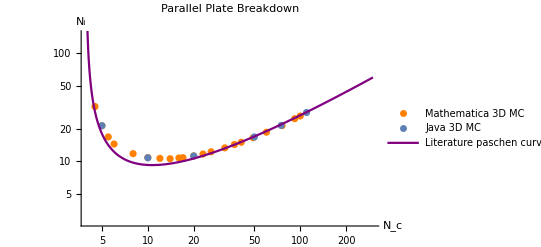

```mathematica
Show[ListLogLogPlot[bdfinal,PlotLegends->{"Mathematica 3D MC"},PlotStyle->Orange],ListLogLogPlot[javabd,PlotLegends->{"Java 3D MC"}],LogLogPlot[0.86*Nc/(Log[Nc]-Log[Log[51]]),{Nc,3.9,300},PlotStyle->Purple,PlotLegends->{"Literature paschen curve"}],PlotRange->{1,5},AxesOrigin->{0.5,1},AxesLabel->{Subscript[N,c],Subscript[N,i]},PlotLabel->"Parallel Plate Breakdown"]
```

## Concentric sphere experiments

```mathematica
t1=Table[AvgElectronsEuler[Nc,1*Nc,5,15,0.5,0.8,False,200] ,{Nc,0.25,8.25}]
```

{1,1.3250.033,2.020.05,2.820.06,4.380.11,6.340.17,8.860.25,12.980.35,18.80.6}

```mathematica
t1=Transpose[{Table[Nc,{Nc,0.25,8.25}],t1}]
```

{{0.25,1},{1.25,1.3250.033},{2.25,2.020.05},{3.25,2.820.06},{4.25,4.380.11},{5.25,6.340.17},{6.25,8.860.25},{7.25,12.980.35},{8.25,18.80.6}}

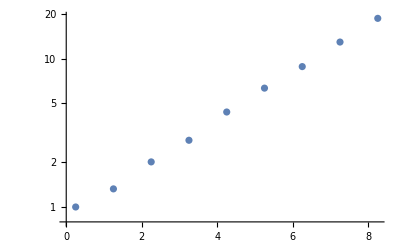

```mathematica
ListLogPlot[t1]
```

```mathematica
t2=Table[AvgElectronsEuler[Nc,2*Nc,5,15,0.5,0.8,False,100] ,{Nc,0.25,8.25}]
```

{1,1.820.08,3.310.16,5.630.30,10.20.6,18.11.1,28.62.0,52.4.,93.7.}

```mathematica
t2=Transpose[{Table[Nc,{Nc,0.25,8.25}],t2}]
```

{{0.25,1},{1.25,1.820.08},{2.25,3.310.16},{3.25,5.630.30},{4.25,10.20.6},{5.25,18.11.1},{6.25,28.62.0},{7.25,52.4.},{8.25,93.7.}}

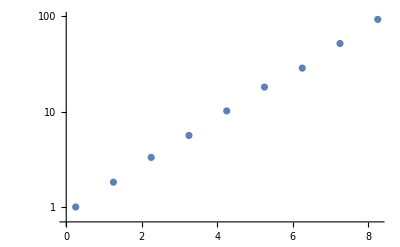

```mathematica
ListLogPlot[t2]
```

```mathematica
t3=Table[{Nc,AvgElectronsEuler[Nc,0.5*Nc,5,15,0.5,0.8,False,200]} ,{Nc,0.25,8.25}]
```

{{0.25,1},{1.25,1},{2.25,1.1500.025},{3.25,1.5300.035},{4.25,1.870.04},{5.25,2.310.05},{6.25,2.710.06},{7.25,3.490.07},{8.25,4.070.09}}

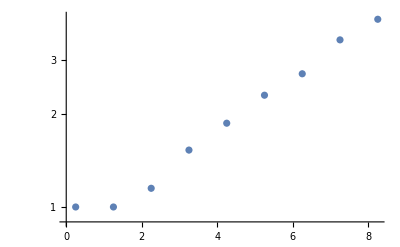

```mathematica
ListLogPlot[t3]
```

```mathematica
AvgElectronsEuler[15,15,5,15,0.5,0.8,False,100]
```

11.470.21

```mathematica
FindBreakdownSS[Nc_,γ_,Ni0_,dt_,reps_]:=Module[{region,list,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
list = Table[{Ni,AvgElectronsEuler[Nc,Ni,5,15,dt,4/5,False,reps]},{Ni,Ni0-3,Ni0+2}];
Print[list];
listForFit = {#[[1]],#[[2,1]]}&/@list;
errorslist = #[[2,2]]&/@list;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
FindNC[Ni_,γ_,Nc0_,dt_,reps_]:=Module[{region,list,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
list = Table[{Nc,AvgElectronsEuler[Nc,Ni,5,15,dt,4/5,False,reps]},{Nc,Nc0-1,Nc0+1,1/2}];
Print[list];
listForFit = {#[[1]],#[[2,1]]}&/@list;
errorslist = #[[2,2]]&/@list;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
FindNC[100,50,4,1/5,300]
```

{{3,18.91.2},{7/2,34.41.9},{4,50.12.8},{9/2,77.4.},{5,130.7.}}

3.970.05

```mathematica
vals2[[2]]
```

Part::partw: Part 2 of {{{3,18.9},{7/2,34.4},{4,50.1},{9/2,77.},{5,130.}}} does not exist.

{{{3,18.91.2},{7/2,34.41.9},{4,50.12.8},{9/2,77.4.},{5,130.7.}}}⟦2⟧

```mathematica
#[[2,2]]&/@vals2
```

{34.41.9}

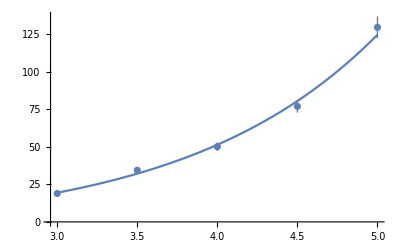

```mathematica
vals2={{3,18.91.2},{7/2,34.41.9},{4,50.12.8},{9/2,77.4.},{5,130.7.}};
fit=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@vals2,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/(#[[2,2]]&/@vals2)^2];
Show[ListPlot[vals2],Plot[fit[x],{x,3,5}]]
```

```mathematica
FindBreakdownSS[5,50,25,2/5,300]
```

{{22,47.02.2},{23,44.02.2},{24,45.92.5},{25,50.32.3},{26,53.82.6},{27,50.62.8},{28,58.93.2}}

25.60.8

```mathematica
FindBreakdownSS[7,50,15,2/5,50]
```

{{12,38.23.4},{13,45.4.},{14,53.6.},{15,58.6.},{16,81.8.},{17,73.9.},{18,93.8.}}

13.580.31

```mathematica
FindBreakdownSS[12,50,8,2/5,50]
```

{{5,4.920.18},{6,7.760.29},{7,12.60.5},{8,18.20.7},{9,25.81.2},{10,40.92.5}}

10.650.15

```mathematica
FindBreakdownSS[30,50,13,2/5,30]
```

{{10,16.91.1},{11,27.41.5},{12,43.02.8},{13,66.4.},{14,99.6.},{15,160.9.}}

12.360.04

```mathematica
FindBreakdownSS[50,50,15,2/5,20]
```

{{12,13.40.9},{13,21.91.6},{14,31.32.2},{15,59.4.},{16,87.5.},{17,129.11.}}

14.830.09

```mathematica
FindBreakdownSS[90,50,19,2/5,20]
```

{{16,13.41.4},{17,21.41.8},{18,36.92.3},{19,45.63.0},{20,71.5.},{21,110.8.}}

19.030.12

```mathematica
FindBreakdownSS[150,50,24,2/5,10]
```

{{21,14.82.5},{22,20.51.5},{23,23.5.},{24,37.5.},{25,42.7.},{26,81.11.}}

25.000.20

```mathematica
ssbd={{4.0360.018,100},{5,25.60.8},{7,13.580.31},{12,10.650.15},{30,12.360.04},{50,14.830.09},{90,19.030.12},{150,25.000.20}}
```

{{4.0360.018,100},{5,25.60.8},{7,13.580.31},{12,10.650.15},{30,12.360.04},{50,14.830.09},{90,19.030.12},{150,25.000.20}}

```mathematica
drwhitmerdata= {{Around[6.493842531696711,0.01909423908773717],15.},{Around[5.4686353869333395,0.01696900035426949],20.},{10,Around[11.227349536224285,0.008038281981665136]},{17.8,Around[11.026218496315959,0.009280574753727079]},{31.6,Around[12.63630851252148,0.0064036079281363555]},{56.2,Around[15.557728814524392,0.019598274560290126]},{100.,Around[20.349828658711385,0.024648429700286353]}}
```

{{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025}}

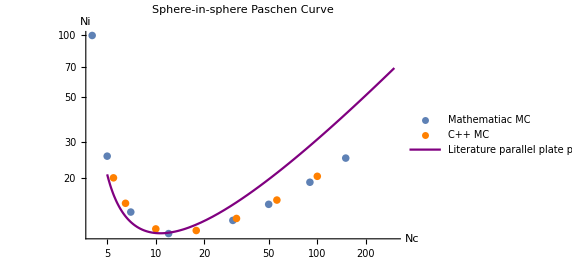

```mathematica
Show[ListLogLogPlot[ssbd,PlotLegends->{"Mathematiac MC"}],ListLogLogPlot[drwhitmerdata,PlotStyle->Orange,PlotLegends->{"C++ MC"}],LogLogPlot[Nc/(Log[Nc]-Log[Log[51]]),{Nc,5,300},PlotStyle->Purple,PlotLegends->{"Literature parallel plate paschen curve"}],AxesLabel->{Nc,Ni},PlotLabel->"Sphere-in-sphere Paschen Curve",PlotRange->All]
```

```mathematica
FindBreakdownSC[λ_,γ_,Ni0_,reps_]:=Module[{region,list,i,errors,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
list = Table[{Ni,MaxElectrons[λ,Ni,reps]},{Ni,Ni0-3,Ni0+3}];
Print[list];
listForFit = {#[[1]],#[[2,1]]}&/@list;
errorslist = #[[2,2]]&/@list;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
FindBreakdownSC[1/2,50,11,20]
```

11.320.07

```mathematica
AvgElectronsEulerSC[1/2,12,15,2/5,4/5,True,20]
```

1000 * RMS travel error: 18.5922

λ: 1/2

Geometry: SC

Collisions: 288.23.

Mean path: 225.756

67.6.

```mathematica
FindBreakdownSC[1,50,15,30]
```

1000 * RMS travel error: 28.422

λ: 1

Geometry: SC

Collisions: 50.6.

Mean path: 32.2375

1000 * RMS travel error: 31.0567

λ: 1

Geometry: SC

Collisions: 53.6.

Mean path: 32.8282

$Aborted

## Sphere-in-cylinder MCs

```mathematica
SCGetNewPositions[Ni_,s_,a_,b_,h_,potential_,x0_,y0_,z0_,vx0_,vy0_,vz0_,cosθ_,ϕ_,ionized_]:=Module[{q,m,path,Δt,x,y,z,vx,vy,vz,ex,ey,ez,Δ,count},
q = 1.60217662 × 10^(-19);
m = 9.10938356 × 10^(-31);
{x,y,z}={x0,y0,z0};
{vx,vy,vz}=SCGetVelocity[vx0,vy0,vz0,cosθ,ϕ,ionized];
path=0;
Δt=0.0000001;
Δ=0.000000000001;
count=0;
Print["new pos"];
While[ path<s ,
If[!(a<=Sqrt[(x+Δt vx)^2+(y+Δt vy)^2+(z+Δt vz)^2]<b-0.005&& -h/2<=(z+Δt vz)<=h/2),Return[{100,100,100,0,0,0}]];
{x,y,z}+=Δt{vx,vy ,vz}; 
Print["iteration"];
{ex,ey,ez}={-(Ni potential[x+Δ,y,z]-Ni potential[x,y,z])/Δ,-(Ni potential[x,y+Δ,z]-Ni potential[x,y,z])/Δ,-(Ni potential[x,y,z+Δ]-Ni potential[x,y,z])/Δ};
{vx,vy,vz}+= ((q Δt)/m){ex,ey,ez }; 
path+=Sqrt[(Δt vx)^2+(Δt vy)^2+(Δt vz)^2];
count++;
];
{x,y,z,vx,vy,vz}]
```

```mathematica
Timing[SCGetNewPositions[5,1,2,7.3,14.6,potential,3,3,3,10000,1000000,10,1,1,False]]
```

new pos

iteration

iteration

iteration

«8 more identical outputs»

{0.000985,{3.0242,3.02483,4.05208,44655.9,45768.9,982059.}}

```mathematica
SCGetVelocity[vx_,vy_,vz_,cosθ_,ϕ_,ionized_]:=Module[{q,m,e0,e1,v0,v1,vx1,vy1,vz1},
q = 1.60217662 × 10^(-19);
m = 9.10938356 × 10^(-31);
v0=Sqrt[vx^2+vy^2+vz^2];
e0=1/2 m v0^2;
If[ionized,
e1=e0-q,
e1 = e0 -q* RandomVariate[UniformDistribution[{0.1,0.5}]]];
If[e1<0,e1=0];
v1=Sqrt[2 e1/m];
vx1 = v1 Cos[ϕ]Sqrt[1-cosθ^2];
vy1 =v1 Sin[ϕ] Sqrt[1-cosθ^2];
vz1=v1 cosθ;{vx1,vy1,vz1}]
```

```mathematica
FindBinNum[costheta_,binwidth_]:=Floor[(costheta+1)/binwidth]+1
```

```mathematica
GetAngles[x_,y_,z_] := {z/Sqrt[x^2+y^2+z^2],ArcTan[x,y]}
```

```mathematica
SCAvgElectrons3D[potential_,a_,b_,h_,Ni_,λ_,binwidth_,lmax_,count_] := Module[{countbin,electronsbin,squaredbin,D,q,result,stack,region,lapl,lbin,lbinSquared,data},
countbin = Table[0,2/binwidth];
electronsbin =  Table[0,2/binwidth];
squaredbin= Table[0,2/binwidth];
lbin = Table[0,lmax/2+1];
lbinSquared =  Table[0,lmax/2+1,lmax/2+1];
data = {};
stack = CreateDataStructure["Stack"];
result = Table[
Module[{x0,y0,z0,x1,y1,z1,numElectrons,currcosθ,currϕ,cθ0,ϕ0,s,vx0,vy0,vz0,vx,vy,vz,r,ionized,z,idx,SH,l,l2},
numElectrons = 1; 
{{x0,y0,z0}}=RandomPoint[Sphere[{0,0,0},a+0.0001],1];
{cθ0,ϕ0} = GetAngles[x0,y0,z0];
stack["Push",{x0,y0,z0,0,0,0}];
While[! stack["EmptyQ"],
{x0,y0,z0,vx,vy,vz}=stack["Pop"];
{currcosθ,currϕ}=GetAngles[x0,y0,z0];
ionized=False;
While[
s=RandomVariate[ExponentialDistribution[1/λ]];
{x1,y1,z1,vx,vy,vz}=SCGetNewPositions[Ni,s,a,b,h,potential,x0,y0,z0,vx,vy,vz,currcosθ,currϕ,ionized];
(a≤Sqrt[x1^2+y1^2+z1^2]≤b&& -h/2≤z1≤h/2),
If[Ni(potential[x0,y0,z0]-potential[x1,y1,z1])≥1,(*fix this*)
{currcosθ,currϕ}=GetAngles[x1,y1,z1];
ionized=True;
numElectrons++;
stack["Push",{x1,y1,z1,0,0,0}],
{currcosθ,currϕ,ionized}={1-2(RandomReal[]),RandomReal[2Pi],False}];
{x0,y0,z0}={x1,y1,z1}
]; 
];
idx=FindBinNum[cθ0,binwidth];
countbin[[idx]]+=1;
electronsbin[[idx]]+=numElectrons;
squaredbin[[idx]]+=numElectrons^2;
SH=numElectrons Table[Conjugate[SphericalHarmonicY[l,0,ArcCos[cθ0],ϕ0]],{l,0,lmax,2}];
AppendTo[data,{ArcCos[cθ0],ϕ0,numElectrons}];
For[l= 0, l <= lmax, l+=2,
lbin[[l/2+1]]+=SH[[l/2+1]];
For[l2=0,l2<=lmax,l2+=2,
lbinSquared[[l/2+1,l2/2+1]]+=SH[[l/2+1]]SH[[l2/2+1]]
]
];
numElectrons],
{count}];
Sow[{countbin,electronsbin, squaredbin,lbin,lbinSquared,data}];Around[Mean[result],StandardDeviation[result]/Sqrt[count]]]
```

## Sphere-in-cylinder experiments

```mathematica
e=Reap[SCAvgElectrons3D[potential,2,7.3,14.6,10,2,0.5,8,1]];
positions={};
collisions={};
ionizations={};
For[i=1,i<=Length[e[[2,1]]],i++,
item = e[[2,1,i]];
If[Equal[item[[1]],"ionization"],If[!Equal[item[[{2,3,4}]],{100,100,100}],AppendTo[ionizations,item[[{2,3,4}]]]];Continue[]];
If[Equal[item[[1]],"collision"],If[!Equal[item[[{2,3,4}]],{100,100,100}],AppendTo[collisions,item[[{2,3,4}]]]], AppendTo[positions,item]]
];
Show[Graphics3D[ {Opacity[0.3],Cylinder[{{0,0,-7.3},{0,0,7.3}},7.3]}],Graphics3D[Ball[{0,0,0},2]],ListLinePlot3D[positions],Graphics3D[{Black,PointSize[0.02],Point[collisions]}],Graphics3D[{Red,PointSize[0.02],Point[ionizations]}]]
```

StandardDeviation::shlen: The argument {7} should have at least two elements.

-Graphics3D-

```mathematica
Show[%632,Boxed->False]
```

-Graphics3D-

```mathematica
SCAvgElectrons3D[potential,3,b_,h_,Ni_,λ_,binwidth_,lmax_,count_]
```

```mathematica
b = Reap[SCAvgElectrons3D[potential,2,7.3,14.6,10,1,0.05,8,100000]];
```

```mathematica
bins=b[[2,1,1]];
```

```mathematica
bins=b[[2,1,1]];
errors =Sqrt[bins[[3]]/bins[[1]] -(bins[[2]]/bins[[1]])^2]/Sqrt[100000];
electronsPart=Table[Around[(bins[[2]]/bins[[1]])[[i]],errors[[i]]],{i,1,40}];
list = bins[[6]];
fit=LinearModelFit[list,Table[SphericalHarmonicY[l,0,θ,ϕ],{l,0,8,2}],{θ,ϕ},IncludeConstantBasis->False];
Clear[t];
max=NMaximize[fit[t,0],{t,0,Pi}];
SHYs=Table[SphericalHarmonicY[l,0,t,0],{l,0,8,2}];
error = Sqrt[SHYs.fit["CovarianceMatrix"].Transpose[SHYs]]/.max[[2]];
Around[max[[1]],error]
electrons=Transpose[{Table[theta,{theta,-0.975,0.975,0.05}],electronsPart}]
Show[Plot[fit[ArcCos[theta],0],{theta,-1,1},PlotRange->{7,10},PlotLegends->{"Spherical Harmonic Function"}],ListPlot[electrons,PlotLegends->{"Electron and cos(θ) bins "}],AxesLabel->{"cos(θ)",Electrons},PlotLabel->"Ionizations across multiple cos(θ) values with prediction"]
```

8.980.10

```mathematica
electrons=Transpose[{Table[theta,{theta,-0.975,0.975,0.05}],electronsPart}]
```

{{-0.975,8.9420.016},{-0.925,8.5520.015},{-0.875,8.3390.014},{-0.825,8.2970.014},{-0.775,8.1600.014},{-0.725,8.2580.014},{-0.675,8.2490.014},{-0.625,8.6040.015},{-0.575,8.3570.015},{-0.525,8.5110.015},{-0.475,8.7560.015},{-0.425,8.6410.015},{-0.375,8.6970.015},{-0.325,8.7680.015},{-0.275,8.7180.015},{-0.225,8.8190.015},{-0.175,8.8080.015},{-0.125,8.9290.015},{-0.075,8.9450.016},{-0.025,8.9130.015},{0.025,8.9600.016},{0.075,8.9780.016},{0.125,8.8490.016},{0.175,8.6930.015},{0.225,8.8260.015},{0.275,8.8680.016},{0.325,8.7890.015},{0.375,8.6890.015},{0.425,8.5330.015},{0.475,8.5740.015},{0.525,8.6320.015},{0.575,8.4490.014},{0.625,8.4230.015},{0.675,8.3220.015},{0.725,8.2710.014},{0.775,8.3070.014},{0.825,8.4180.014},{0.875,8.4030.014},{0.925,8.5520.015},{0.975,8.7680.015}}

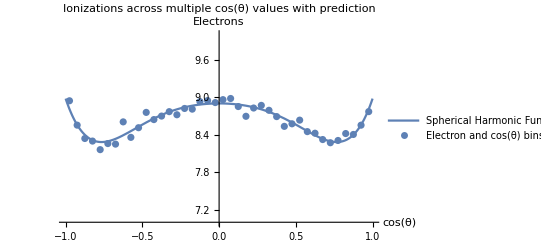

```mathematica
Show[Plot[fit[ArcCos[theta],0],{theta,-1,1},PlotRange->{7,10},PlotLegends->{"Spherical Harmonic Function"}],ListPlot[electrons,PlotLegends->{"Electron and cos(θ) bins "}],AxesLabel->{"cos(θ)",Electrons},PlotLabel->"Ionizations across multiple cos(θ) values with prediction"]
```

```mathematica
MaxElectrons[potential_,Ni_,a_,b_,h_,λ_,lmax_,reps_]:= Module[{idx,errors,electronsPart,list, bins,i,thetaslist,constants,SHYs,fit,max,error},
bins =Last[Last[Last[Reap[SCAvgElectrons3D[potential,a,b,h,Ni,λ,0.2,lmax,reps]]]]];
errors =Sqrt[bins[[3]]/bins[[1]] -(bins[[2]]/bins[[1]])^2]/Sqrt[reps];
electronsPart=Table[Around[(bins[[2]]/bins[[1]])[[i]],errors[[i]]],{i,1,10}];
list = bins[[6]];
fit=LinearModelFit[list,Table[SphericalHarmonicY[l,0,θ,ϕ],{l,0,lmax,2}],{θ,ϕ},IncludeConstantBasis->False];
Clear[t];
max=NMaximize[fit[t,0],{t,0,Pi}];
SHYs=Table[SphericalHarmonicY[l,0,t,0],{l,0,lmax,2}];
error = Sqrt[SHYs.fit["CovarianceMatrix"].Transpose[SHYs]]/.max[[2]];
Around[max[[1]],error]
]
```

## Sphere-in-cylinder breakdown plotting

```mathematica
FindBreakdownSC[a_,b_,h_,potential_,Ni0_,λ_,γ_,reps_]:=Module[{region,lapl,maxes,i,errors,list,max,params,fit,error,p1,p2,p3,p4,f,vals,errorslist,listForFit},
maxes = Table[{Ni,MaxElectrons[potential,Ni,a,b,h,λ,6,reps]},{Ni,Ni0-3,Ni0+2}];
listForFit = {#[[1]],#[[2,1]]}&/@maxes;
errorslist = #[[2,2]]&/@maxes;
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
Print[fit["BestFitParameters"]];
f=(Log[(γ-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
Around[f,Sqrt[error]]/.fit["BestFitParameters"]
]
```

```mathematica
Clear[f]
region=RegionDifference[Cylinder[{{0,0,-7.3},{0,0,7.3}},7.3],Ball[{0,0,0},2]];
lapl=Laplacian[f[x,y,z],{x,y,z}]==0;
potential=NDSolveValue[{lapl,DirichletCondition[f[x,y,z]==1,x^2+y^2+z^2<7],DirichletCondition[f[x,y,z]==0,x^2+y^2+z^2>=7]},f,{x,y,z}∈region,AccuracyGoal->3.3]
```

InterpolatingFunction[{{-7.29819, 7.3}, {-7.29955, 7.29955}, {-7.3, 7.3}}, <>]

```mathematica
SCAvgElectrons3D[potential,2,7.3,14.6,3,1,0.5,8,3]
```

new pos

new pos

new pos

«36 more identical outputs»

2

```mathematica
maxes=Table[{Ni,MaxElectrons[potential,Ni,2,7.3,14.6,1/2,8,5000]},{Ni, 10, 16}]
```

{{10,11.960.18},{11,14.40.6},{12,19.060.33},{13,24.51.0},{14,29.20.5},{15,34.60.6},{16,43.60.8}}

```mathematica
listForFit = {#[[1]],#[[2,1]]}&/@maxes;
errorslist = #[[2,2]]&/@maxes;
Clear[p1, p2, p3];
fit=NonlinearModelFit[listForFit,p1 Exp[p2 x]+p3,{p1, p2, p3}, x,Weights->1/errorslist^2];
Print[fit["BestFitParameters"]];
f=(Log[(25-p3)/p1]/p2);
error={D[f,p1],D[f,p2],D[f,p3]}.fit["CovarianceMatrix"].Transpose[{D[f,p1],D[f,p2],D[f,p3]}]/.fit["BestFitParameters"];
res=Around[f,Sqrt[error]]/.fit["BestFitParameters"]
```

{p1→2.99664,p2→0.173537,p3→-5.05554}

13.290.06

{p1→0.658244,p2→0.248882,p3→2.9867}

{p1→1.42681,p2→0.206204,p3→-0.0785481}

13.900.18

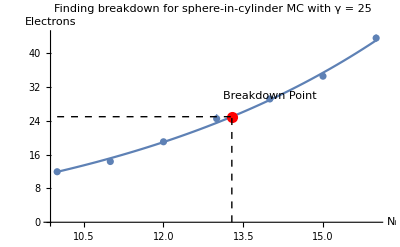

```mathematica
Show[ListPlot[maxes],Plot[fit[x],{x,10,16}],Graphics[{Red,PointSize[0.02],Point[{res[[1]],25}]}],Graphics[{Dashed,Black,Line[{{10,25},{res[[1]],25}}],Line[{{res[[1]],0},{res[[1]],25}}]}],Graphics[Text[Breakdown Point,{14,30}]],AxesLabel->{Subscript[N,i],Electrons},PlotLabel->"Finding breakdown for sphere-in-cylinder MC with γ = 25"]
```

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,35,1.25,25,15000]
```

{p1$28058650→0.000237721,p2$28058650→0.269744,p3$28058650→23.2491}

33.00.6

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,20,1,25,5000]
```

{p1$40305517→0.132615,p2$40305517→0.209131,p3$40305517→14.8328}

20.750.12

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,15,1/1.5,25,1000]
```

{p1$45373512→1.1035,p2$45373512→0.198064,p3$45373512→5.66513}

14.460.07

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,13,1/2,25,600]
```

{p1$47267324→0.0564577,p2$47267324→0.418192,p3$47267324→9.50659}

13.430.12

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,13,1/3,25,600]
```

{p1$48672330→0.230411,p2$48672330→0.337474,p3$48672330→3.99531}

13.370.07

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,14,1/4,25,500]
```

{p1$50934646→0.177758,p2$50934646→0.345819,p3$50934646→4.20329}

13.770.10

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,14,1/5,25,300]
```

{p1$53857265→0.559107,p2$53857265→0.274326,p3$53857265→-3.06715}

14.280.06

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,16,1/6,25,300]
```

{p1$55698439→0.175876,p2$55698439→0.325052,p3$55698439→0.181037}

15.230.07

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,16,1/7,25,200]
```

{p1$58874944→0.198238,p2$58874944→0.300782,p3$58874944→0.351914}

16.030.12

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,17,1/8,25,100]
```

{p1$60897865→0.210061,p2$60897865→0.289947,p3$60897865→-1.55746}

16.690.11

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,18,1/9,25,100]
```

{p1$62135782→3.85643,p2$62135782→0.140954,p3$62135782→-20.3661}

17.50.4

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,19,1/10,25,50]
```

{p1$63550115→0.0205091,p2$63550115→0.385069,p3$63550115→2.58807}

18.170.20

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,21,1/11,25,250]
```

{p1$64381687→0.000626241,p2$64381687→0.519007,p3$64381687→10.4727}

19.370.11

```mathematica
FindBreakdownSC[2,7.3,14.6,potential,21,1/12,25,50]
```

{p1$81328072→1.21196×10^-7,p2$81328072→0.897943,p3$81328072→16.4739}

20.120.20

```mathematica
res={{1/1.25,33.00.6},{1,20.750.12},{1.5, 14.460.07},{2,13.430.12},{3,13.370.07},{4,13.770.10},{5,14.280.06},{6,15.230.07},{7,16.030.12},{8,16.690.11},{9,17.50.4},{10,18.170.20},{11,19.370.11},{12,20.120.20}}
```

{{0.8,33.00.6},{1,20.750.12},{1.5,14.460.07},{2,13.430.12},{3,13.370.07},{4,13.770.10},{5,14.280.06},{6,15.230.07},{7,16.030.12},{8,16.690.11},{9,17.50.4},{10,18.170.20},{11,19.370.11},{12,20.120.20}}

```mathematica
"1/λ (log scale)"
```

1/λ (log scale)

```mathematica
listforfit = {#[[1]],#[[2,1]]}&/@res
```

{{0.8,33.011},{1,20.75},{1.5,14.457},{2,13.4261},{3,13.3718},{4,13.7706},{5,14.275},{6,15.227},{7,16.0348},{8,16.6915},{9,17.4882},{10,18.1694},{11,19.3674}}

```mathematica
NonlinearModelFit[listforfit,a Nc/(Log[a Nc]-Log[Log[51]]),a,Nc]
```

FittedModel[(1.11453 Nc)/(Log[1.11453 Nc]-Log[Log[51]])]

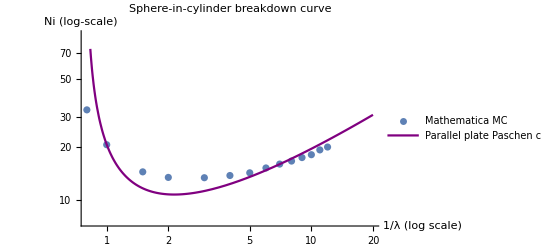

```mathematica
Show[ListLogLogPlot[res,PlotLegends->{"Mathematica MC"}],LogLogPlot[5Nc/(Log[5Nc]-Log[Log[51]]),{Nc,0.5,20},PlotStyle->Purple,PlotLegends->{"Parallel plate Paschen curve"}],PlotLabel->"Sphere-in-cylinder breakdown curve",AxesLabel->{"1/λ (log scale)", "Ni (log-scale)"},PlotRange->{2,4.5},AxesOrigin->{-0.5,2}]
```

## Plotting fusor data

```mathematica
data=Import["/Users/wbowers/Downloads/RAWpaschendata.txt","Table"]
```

{{----------,--------},{17.4373,2086.77},{17.4627,2052.92},{17.4878,2069.5},{17.5153,2036.34},{17.549,2081.93},{17.5836,2041.17},{17.6141,2037.03},{17.641,2048.08},{17.6684,2031.5},7155,{16663.4,2073.64},{16666.9,2081.24},{16670.7,2081.24},{16677.3,2079.17},{16684,2102.66},{16690.9,2073.64},{16697.9,2077.79},{16704.9,2082.62},{----------,--------}}
 |  |  |  |

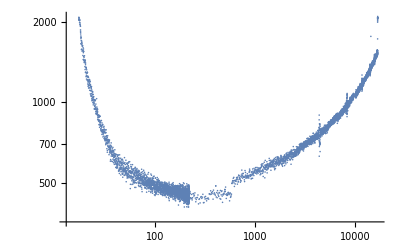

```mathematica
ListLogLogPlot[data]
```

```mathematica
FindMinimum[30x/Log[x]-3,{x,2}]
```

{78.5485,{x→2.71828}}

```mathematica
b = 365
```

365

```mathematica
a = 15
```

15

```mathematica
k = Log[a / Log[1+1/(0.01)]]
```

1.17871

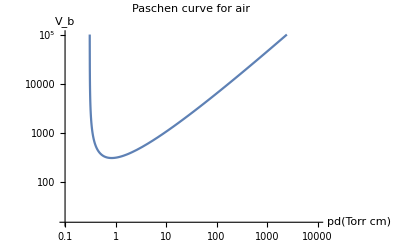

```mathematica
LogLogPlot[b x/(Log[x]+k),{x,0.1,10000},PlotRange->{{0.1,10000},{15,100000}},AxesOrigin->{0.1,15},PlotLabel->"Paschen curve for air",AxesLabel->{"pd(Torr cm)" , Subscript[V, "b"]}]
```

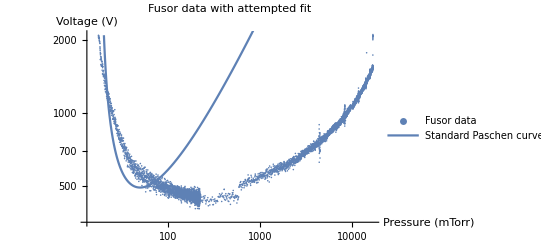

```mathematica
Show[ListLogLogPlot[data,PlotLegends->{"Fusor data"}],LogLogPlot[10x/(Log[x]-2.9),{x,20,1000},PlotLegends->{"Standard Paschen curve"}],AxesLabel->{"Pressure (mTorr)","Voltage (V)"},PlotLabel->"Fusor data with attempted fit"]
```

## Visualizing geometries

```mathematica
Show[Graphics3D[{Opacity[0.5],Sphere[{0,0,0},5]}],Graphics3D[{Opacity[0.5],Sphere[{0,0,0},2]}],Graphics3D[{Thick,Dashed,Red,Line[{{0,0,0},{5,0,1}}]}],Graphics3D[{Thick,Dashed,Blue,Line[{{0,0,0},{2,0,-0.5}}]}],Graphics3D[{Text[Style["a",Larger,Italic],{0.75,0,-0.75}],Text[Style["b",Larger,Italic],{3.25,0,1.25}]}],PlotLabel->"Visualization of Concentric Spheres Setup",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{Opacity[0.5],Cylinder[{{0,0,-5},{0,0,5}},5]}],Graphics3D[{Opacity[0.5],Sphere[{0,0,0},2]}],Graphics3D[{Thick,Dashed,Red,Line[{{0,0,0},{5,0,0}}]}],Graphics3D[{Thick,Dashed,Blue,Line[{{0,0,0},{2,0,-0.5}}]}],Graphics3D[{Thick,Dashed,Purple,Line[{{0,0,0},{0,0,5}}]}],Graphics3D[{Text[Style["a",Larger,Italic],{0.75,0,-0.75}],Text[Style["b",Larger,Italic],{3.25,0,0.65}],Text[Style["h / 2",Larger,Italic],{0.8,0,3}]}],PlotLabel->"Visualization of Sphere-in-Cylinder Setup",AxesLabel->Automatic]
```

-Graphics3D-